## day

```mathematica
szdirectory=".wine/drive_c/new_xdzq_tyrz/vipdoc/sz/lday/";
shdirectory=".wine/drive_c/new_xdzq_tyrz/vipdoc/sh/lday/";
stock[str_]:=If[StringStartsQ[str,"sz"],szdirectory~~str~~".day",shdirectory~~str~~".day"];
```

```mathematica
head={"Day","O","H","L","C","Amount","Vol","Flag"};
data=BinaryReadList[stock["sz000001"],{"Integer32","Integer32","Integer32","Integer32","Integer32","Real32","Integer32","Integer32"}];
data[[All,6]]=IntegerPart[data[[All,6]]];
TableForm[data,TableHeadings->{None,head}]
```

Day | O | H | L | C | Amount | Vol | Flag
20130902 | 1074 | 1083 | 1063 | 1075 | 537024128 | 50023178 | 65536
20130903 | 1079 | 1120 | 1072 | 1120 | 1276796928 | 115757165 | 65536
20130904 | 1116 | 1140 | 1105 | 1108 | 1001844672 | 89262009 | 65536
20130905 | 1108 | 1113 | 1098 | 1103 | 379657120 | 34323007 | 65536
20130909 | 1128 | 1213 | 1128 | 1213 | 2639382272 | 220449384 | 65536
20130910 | 1242 | 1265 | 1199 | 1244 | 2574801664 | 208529430 | 65536
20130911 | 1240 | 1315 | 1220 | 1269 | 2186675968 | 170823000 | 65536
20130912 | 1252 | 1386 | 1240 | 1347 | 2418432512 | 183054040 | 65536
20130913 | 1323 | 1370 | 1303 | 1321 | 1587326720 | 119131992 | 65536
20130916 | 1322 | 1364 | 1267 | 1320 | 1874388864 | 143436615 | 65536
20130917 | 1315 | 1337 | 1275 | 1279 | 1224996864 | 94002603 | 65536
20130918 | 1275 | 1299 | 1251 | 1279 | 786897792 | 61700281 | 65536
20130923 | 1280 | 1297 | 1262 | 1288 | 928672768 | 72379517 | 65536
20130924 | 1286 | 1287 | 1197 | 1227 | 1786488320 | 145618921 | 65536
20130925 | 1218 | 1245 | 1198 | 1203 | 949782720 | 77993068 | 65536
20130926 | 1196 | 1196 | 1150 | 1166 | 1002417088 | 86071180 | 65536
20130927 | 1163 | 1201 | 1160 | 1190 | 810756864 | 68751989 | 65536
20130930 | 1190 | 1204 | 1182 | 1188 | 445333344 | 37360168 | 65536
20131008 | 1188 | 1234 | 1151 | 1221 | 888899072 | 73757471 | 65536
20131009 | 1212 | 1275 | 1202 | 1255 | 1054297728 | 84408432 | 65536
20131010 | 1260 | 1275 | 1220 | 1228 | 967348800 | 77626822 | 65536
20131011 | 1241 | 1278 | 1236 | 1269 | 1165261952 | 92298675 | 65536
20131014 | 1260 | 1269 | 1247 | 1249 | 693548160 | 55293904 | 65536
20131015 | 1249 | 1250 | 1213 | 1221 | 594407040 | 48446347 | 65536
20131016 | 1215 | 1216 | 1193 | 1201 | 544119424 | 45239616 | 65536
20131017 | 1213 | 1224 | 1200 | 1200 | 378747296 | 31361587 | 65536
20131018 | 1201 | 1244 | 1196 | 1220 | 631501184 | 51565253 | 65536
20131021 | 1221 | 1238 | 1202 | 1233 | 736781248 | 60301258 | 65536
20131022 | 1228 | 1228 | 1201 | 1205 | 623986688 | 51490012 | 65536
20131023 | 1217 | 1316 | 1216 | 1258 | 1957187840 | 154335727 | 65536
20131024 | 1261 | 1315 | 1240 | 1300 | 1909977856 | 147778442 | 65536
20131025 | 1293 | 1380 | 1286 | 1343 | 1935859072 | 144110740 | 65536
20131028 | 1340 | 1342 | 1297 | 1313 | 1154607616 | 87876298 | 65536
20131029 | 1315 | 1440 | 1315 | 1412 | 2981260800 | 214154014 | 65536
20131030 | 1400 | 1449 | 1381 | 1440 | 1871874560 | 132582234 | 65536
20131031 | 1425 | 1432 | 1375 | 1390 | 1558479744 | 111296872 | 65536
20131101 | 1388 | 1411 | 1365 | 1387 | 1175747328 | 84492161 | 65536
20131104 | 1398 | 1409 | 1347 | 1356 | 1013876800 | 73966847 | 65536
20131105 | 1330 | 1369 | 1296 | 1366 | 1305185664 | 98703535 | 65536
20131106 | 1341 | 1348 | 1306 | 1315 | 951290048 | 71528944 | 65536
20131107 | 1321 | 1346 | 1310 | 1327 | 913998400 | 68650390 | 65536
20131108 | 1310 | 1354 | 1308 | 1333 | 958253504 | 72008185 | 65536
20131111 | 1333 | 1354 | 1310 | 1340 | 823194176 | 61585088 | 65536
20131112 | 1341 | 1410 | 1341 | 1405 | 1510757376 | 108732646 | 65536
20131113 | 1387 | 1393 | 1327 | 1333 | 1127155584 | 82642150 | 65536
20131114 | 1325 | 1336 | 1297 | 1314 | 1262294144 | 96441257 | 65536
20131115 | 1318 | 1377 | 1306 | 1336 | 1306569856 | 96702975 | 65536
20131118 | 1348 | 1414 | 1325 | 1409 | 1761157760 | 128156183 | 65536
20131119 | 1404 | 1412 | 1377 | 1382 | 1161254272 | 83538392 | 65536
20131120 | 1400 | 1420 | 1375 | 1399 | 984763584 | 70523848 | 65536
20131121 | 1387 | 1396 | 1348 | 1394 | 1289349376 | 94467419 | 65536
20131122 | 1388 | 1390 | 1367 | 1367 | 741591616 | 53878412 | 65536
20131125 | 1340 | 1379 | 1336 | 1350 | 722870912 | 53232867 | 65536
20131126 | 1350 | 1363 | 1340 | 1347 | 528774464 | 39201960 | 65536
20131127 | 1341 | 1382 | 1337 | 1357 | 783820160 | 57665667 | 65536
20131128 | 1357 | 1379 | 1354 | 1362 | 845915776 | 61904047 | 65536
20131129 | 1380 | 1389 | 1356 | 1360 | 850388544 | 62016341 | 65536
20131202 | 1364 | 1406 | 1355 | 1375 | 1682918400 | 122233192 | 65536
20131203 | 1368 | 1382 | 1330 | 1354 | 1081622656 | 80243605 | 65536
20131204 | 1350 | 1385 | 1336 | 1360 | 1217121536 | 89180491 | 65536
20131205 | 1358 | 1362 | 1337 | 1343 | 818132160 | 60748011 | 65536
20131206 | 1347 | 1348 | 1324 | 1329 | 640155456 | 48110321 | 65536
20131209 | 1330 | 1339 | 1318 | 1319 | 553192448 | 41804455 | 65536
20131210 | 1330 | 1334 | 1320 | 1329 | 429632576 | 32403351 | 65536
20131211 | 1320 | 1324 | 1268 | 1284 | 1192542592 | 92520405 | 65536
20131212 | 1271 | 1287 | 1266 | 1272 | 507708736 | 39806210 | 65536
20131213 | 1268 | 1269 | 1245 | 1255 | 540933952 | 43034386 | 65536
20131216 | 1250 | 1283 | 1250 | 1275 | 704816704 | 55566784 | 65536
20131217 | 1279 | 1288 | 1262 | 1272 | 470046208 | 36768042 | 65536
20131218 | 1270 | 1285 | 1265 | 1276 | 296740192 | 23274046 | 65536
20131219 | 1278 | 1285 | 1250 | 1250 | 450676320 | 35620149 | 65536
20131220 | 1251 | 1258 | 1191 | 1191 | 826323840 | 68133392 | 65536
20131223 | 1192 | 1218 | 1180 | 1195 | 495535264 | 41215329 | 65536
20131224 | 1200 | 1212 | 1160 | 1170 | 617009152 | 51936463 | 65536
20131225 | 1170 | 1179 | 1153 | 1172 | 589596288 | 50589941 | 65536
20131226 | 1170 | 1170 | 1143 | 1145 | 463847168 | 40230092 | 65536
20131227 | 1146 | 1189 | 1143 | 1175 | 733105792 | 63066168 | 65536
20131230 | 1179 | 1185 | 1170 | 1174 | 512282784 | 43574488 | 65536
20131231 | 1173 | 1239 | 1165 | 1225 | 1002632448 | 82686418 | 65536
20140102 | 1212 | 1230 | 1205 | 1223 | 596223744 | 48991089 | 65536
20140103 | 1215 | 1216 | 1178 | 1193 | 656631296 | 55111484 | 65536
20140106 | 1189 | 1200 | 1150 | 1167 | 679280384 | 58211823 | 65536
20140107 | 1153 | 1176 | 1151 | 1163 | 393977568 | 33840749 | 65536
20140108 | 1164 | 1195 | 1153 | 1176 | 538436160 | 45776816 | 65536
20140109 | 1169 | 1199 | 1165 | 1182 | 576870528 | 48551836 | 65536
20140110 | 1178 | 1195 | 1166 | 1182 | 450487744 | 38119765 | 65536
20140113 | 1180 | 1191 | 1149 | 1160 | 559375168 | 47887517 | 65536
20140114 | 1157 | 1178 | 1145 | 1172 | 420715264 | 36242708 | 65536
20140115 | 1170 | 1174 | 1156 | 1167 | 346733024 | 29798810 | 65536
20140116 | 1166 | 1180 | 1158 | 1169 | 350027744 | 29959340 | 65536
20140117 | 1162 | 1164 | 1145 | 1148 | 487423200 | 42351387 | 65536
20140120 | 1148 | 1148 | 1125 | 1130 | 349154112 | 30721993 | 65536
20140121 | 1132 | 1156 | 1132 | 1136 | 303578624 | 26579498 | 65536
20140122 | 1136 | 1186 | 1135 | 1179 | 723523200 | 61908449 | 65536
20140123 | 1177 | 1179 | 1165 | 1170 | 439497024 | 37553549 | 65536
20140124 | 1164 | 1181 | 1157 | 1166 | 567516096 | 48528331 | 65536
20140127 | 1156 | 1163 | 1135 | 1139 | 508343008 | 44299725 | 65536
20140128 | 1145 | 1159 | 1137 | 1150 | 446213152 | 38968302 | 65536
20140129 | 1154 | 1164 | 1150 | 1156 | 361575328 | 31210441 | 65536
20140130 | 1155 | 1155 | 1138 | 1140 | 332618208 | 29141306 | 65536
20140207 | 1132 | 1138 | 1110 | 1138 | 470138336 | 41875743 | 65536
20140210 | 1138 | 1159 | 1135 | 1157 | 670008704 | 58122625 | 65536
20140211 | 1153 | 1233 | 1143 | 1200 | 1569553152 | 131046538 | 65536
20140212 | 1187 | 1220 | 1185 | 1194 | 831733248 | 69462197 | 65536
20140213 | 1183 | 1250 | 1180 | 1222 | 1480576896 | 121819274 | 65536
20140214 | 1211 | 1219 | 1196 | 1208 | 701905728 | 58233934 | 65536
20140217 | 1210 | 1217 | 1187 | 1197 | 727601216 | 60892188 | 65536
20140218 | 1191 | 1193 | 1162 | 1166 | 700246016 | 59606163 | 65536
20140219 | 1161 | 1213 | 1161 | 1200 | 1177763456 | 98817485 | 65536
20140220 | 1193 | 1225 | 1175 | 1176 | 919006400 | 76632414 | 65536
20140221 | 1182 | 1184 | 1158 | 1160 | 559681280 | 47999662 | 65536
20140224 | 1145 | 1148 | 1114 | 1116 | 750803456 | 66782028 | 65536
20140225 | 1117 | 1135 | 1100 | 1102 | 611611840 | 54838742 | 65536
20140226 | 1103 | 1122 | 1100 | 1111 | 453164480 | 40793776 | 65536
20140227 | 1115 | 1135 | 1101 | 1124 | 621811136 | 55508601 | 65536
20140228 | 1117 | 1124 | 1088 | 1113 | 493549152 | 44623752 | 65536
20140303 | 1102 | 1108 | 1093 | 1104 | 470295904 | 42743198 | 65536
20140304 | 1099 | 1102 | 1080 | 1098 | 575054336 | 52758525 | 65536
20140305 | 1089 | 1098 | 1063 | 1070 | 575251328 | 53301669 | 65536
20140306 | 1071 | 1085 | 1051 | 1077 | 564310336 | 52738264 | 65536
20140307 | 1075 | 1094 | 1072 | 1080 | 529718080 | 48865432 | 65536
20140310 | 1070 | 1072 | 1025 | 1031 | 567573120 | 54432074 | 65536
20140311 | 1031 | 1039 | 1010 | 1024 | 462135328 | 45078939 | 65536
20140312 | 1027 | 1048 | 1018 | 1035 | 532491168 | 51510718 | 65536
20140313 | 1048 | 1079 | 1037 | 1056 | 663461504 | 62662521 | 65536
20140314 | 1043 | 1053 | 1027 | 1032 | 466403744 | 45039250 | 65536
20140317 | 1041 | 1050 | 1034 | 1047 | 388751072 | 37297944 | 65536
20140318 | 1047 | 1051 | 1033 | 1038 | 449377632 | 43181485 | 65536
20140319 | 1035 | 1035 | 1015 | 1024 | 370332000 | 36302890 | 65536
20140320 | 1022 | 1029 | 1005 | 1010 | 462702976 | 45488151 | 65536
20140321 | 1007 | 1094 | 1003 | 1079 | 1316754816 | 125181194 | 65536
20140324 | 1077 | 1093 | 1063 | 1079 | 908755200 | 84253869 | 65536
20140325 | 1077 | 1081 | 1056 | 1060 | 444839360 | 41575437 | 65536
20140326 | 1066 | 1075 | 1054 | 1070 | 383229632 | 36020600 | 65536
20140327 | 1064 | 1103 | 1052 | 1077 | 867999424 | 80313368 | 65536
20140328 | 1070 | 1096 | 1067 | 1078 | 576611648 | 53264990 | 65536
20140331 | 1085 | 1094 | 1067 | 1077 | 346029600 | 32113078 | 65536
20140401 | 1072 | 1089 | 1070 | 1080 | 303939584 | 28124287 | 65536
20140402 | 1079 | 1101 | 1073 | 1091 | 500530400 | 46039729 | 65536
20140403 | 1096 | 1102 | 1076 | 1077 | 494227840 | 45365089 | 65536
20140404 | 1070 | 1082 | 1059 | 1079 | 366585728 | 34209026 | 65536
20140408 | 1078 | 1149 | 1078 | 1128 | 1503024000 | 134292058 | 65536
20140409 | 1127 | 1135 | 1116 | 1119 | 626176128 | 55734652 | 65536
20140410 | 1121 | 1160 | 1116 | 1136 | 876017984 | 77006827 | 65536
20140411 | 1134 | 1150 | 1125 | 1140 | 674562240 | 59325527 | 65536
20140414 | 1135 | 1145 | 1119 | 1128 | 476278752 | 42174131 | 65536
20140415 | 1121 | 1123 | 1091 | 1097 | 589940416 | 53468878 | 65536
20140416 | 1093 | 1113 | 1086 | 1099 | 414021984 | 37664608 | 65536
20140417 | 1102 | 1108 | 1083 | 1090 | 333305056 | 30488525 | 65536
20140418 | 1085 | 1088 | 1072 | 1080 | 349102656 | 32354412 | 65536
20140421 | 1075 | 1090 | 1067 | 1069 | 321959264 | 29815603 | 65536
20140422 | 1071 | 1118 | 1068 | 1106 | 569433664 | 52328164 | 65536
20140423 | 1108 | 1145 | 1108 | 1130 | 1346115072 | 119102811 | 65536
20140424 | 1142 | 1145 | 1112 | 1123 | 712292416 | 63400485 | 65536
20140425 | 1123 | 1152 | 1111 | 1125 | 810796672 | 71433523 | 65536
20140428 | 1125 | 1128 | 1096 | 1103 | 582533632 | 52604503 | 65536
20140429 | 1102 | 1125 | 1092 | 1116 | 458216064 | 41362159 | 65536
20140430 | 1118 | 1122 | 1109 | 1114 | 289386176 | 25959642 | 65536
20140505 | 1110 | 1111 | 1083 | 1099 | 440413664 | 40327050 | 65536
20140506 | 1092 | 1109 | 1090 | 1095 | 294197728 | 26777091 | 65536
20140507 | 1091 | 1095 | 1085 | 1085 | 263547088 | 24191029 | 65536
20140508 | 1083 | 1115 | 1081 | 1093 | 418459584 | 37962091 | 65536
20140509 | 1093 | 1113 | 1090 | 1105 | 354936704 | 32191490 | 65536
20140512 | 1115 | 1140 | 1102 | 1134 | 678608640 | 60199194 | 65536
20140513 | 1133 | 1136 | 1119 | 1123 | 344109440 | 30583330 | 65536
20140514 | 1121 | 1144 | 1121 | 1131 | 471890560 | 41612180 | 65536
20140515 | 1130 | 1135 | 1115 | 1119 | 351067744 | 31262755 | 65536
20140516 | 1119 | 1134 | 1118 | 1127 | 351626464 | 31177310 | 65536
20140519 | 1127 | 1128 | 1114 | 1127 | 292426272 | 26110555 | 65536
20140520 | 1125 | 1134 | 1117 | 1124 | 231625056 | 20576600 | 65536
20140521 | 1120 | 1138 | 1108 | 1133 | 297218368 | 26316829 | 65536
20140522 | 1133 | 1166 | 1129 | 1139 | 713100736 | 61914166 | 65536
20140523 | 1140 | 1161 | 1136 | 1158 | 478107232 | 41535649 | 65536
20140526 | 1165 | 1165 | 1146 | 1158 | 365020288 | 31598919 | 65536
20140527 | 1153 | 1170 | 1150 | 1158 | 329865248 | 28440770 | 65536
20140528 | 1157 | 1163 | 1139 | 1160 | 491816864 | 42703763 | 65536
20140529 | 1159 | 1174 | 1149 | 1150 | 420664544 | 36223849 | 65536
20140530 | 1149 | 1162 | 1146 | 1150 | 367350848 | 31877309 | 65536
20140603 | 1150 | 1169 | 1150 | 1151 | 322371200 | 27811387 | 65536
20140604 | 1151 | 1152 | 1125 | 1133 | 367011936 | 32388974 | 65536
20140605 | 1130 | 1144 | 1129 | 1143 | 280049632 | 24629125 | 65536
20140606 | 1144 | 1148 | 1129 | 1138 | 212129088 | 18643555 | 65536
20140609 | 1135 | 1154 | 1132 | 1148 | 359580576 | 31352202 | 65536
20140610 | 1152 | 1175 | 1147 | 1175 | 723590272 | 62198265 | 65536
20140611 | 1168 | 1184 | 1163 | 1178 | 509141984 | 43323327 | 65536
20140612 | 962 | 977 | 960 | 971 | 355905024 | 36744198 | 65536
20140613 | 970 | 1038 | 968 | 1012 | 1246107264 | 123950476 | 65536
20140616 | 1006 | 1024 | 1002 | 1013 | 889629952 | 87818234 | 65536
20140617 | 1005 | 1018 | 998 | 1004 | 546274880 | 54184787 | 65536
20140618 | 1004 | 1006 | 981 | 986 | 534087744 | 53855012 | 65536
20140619 | 986 | 994 | 968 | 978 | 474545248 | 48308104 | 65536
20140620 | 977 | 985 | 974 | 985 | 364389984 | 37207089 | 65536
20140623 | 985 | 995 | 976 | 977 | 423339296 | 43085977 | 65536
20140624 | 978 | 985 | 976 | 980 | 279235072 | 28459321 | 65536
20140625 | 980 | 981 | 964 | 977 | 263555600 | 27126263 | 65536
20140626 | 971 | 983 | 971 | 982 | 335699968 | 34288524 | 65536
20140627 | 979 | 987 | 971 | 982 | 359856064 | 36752084 | 65536
20140630 | 980 | 997 | 979 | 991 | 442037472 | 44723794 | 65536
20140701 | 991 | 995 | 983 | 986 | 281216672 | 28494372 | 65536
20140702 | 986 | 990 | 981 | 989 | 281857216 | 28604171 | 65536
20140703 | 989 | 999 | 983 | 996 | 443709920 | 44690486 | 65536
20140704 | 997 | 1001 | 986 | 991 | 339852544 | 34231126 | 65536
20140707 | 991 | 993 | 980 | 986 | 337859968 | 34306164 | 65536
20140708 | 984 | 993 | 977 | 993 | 341179840 | 34608702 | 65536
20140709 | 992 | 992 | 958 | 965 | 573417344 | 58789114 | 65536
20140710 | 966 | 973 | 961 | 967 | 348040192 | 36025783 | 65536
20140711 | 966 | 970 | 964 | 967 | 307776992 | 31832009 | 65536
20140714 | 968 | 972 | 957 | 972 | 446246592 | 46311613 | 65536
20140716 | 970 | 971 | 952 | 961 | 592431488 | 61770283 | 65536
20140717 | 960 | 962 | 953 | 959 | 306409312 | 32007282 | 65536
20140718 | 955 | 965 | 953 | 960 | 360507392 | 37511523 | 65536
20140721 | 960 | 960 | 953 | 955 | 260823472 | 27299506 | 65536
20140722 | 953 | 980 | 952 | 973 | 594111744 | 61369888 | 65536
20140723 | 970 | 983 | 968 | 976 | 541821248 | 55570368 | 65536
20140724 | 977 | 1030 | 976 | 1016 | 1820306688 | 180582397 | 65536
20140725 | 1020 | 1026 | 1008 | 1022 | 868778304 | 85391389 | 65536
20140728 | 1026 | 1090 | 1024 | 1078 | 1997922432 | 186787917 | 65536
20140729 | 1082 | 1110 | 1073 | 1082 | 1306061696 | 120182708 | 65536
20140730 | 1082 | 1110 | 1073 | 1075 | 880625344 | 81002561 | 65536
20140731 | 1075 | 1090 | 1065 | 1087 | 685541120 | 63778443 | 65536
20140801 | 1084 | 1108 | 1070 | 1070 | 930971520 | 85450966 | 65536
20140804 | 1070 | 1093 | 1060 | 1093 | 896723520 | 83062393 | 65536
20140805 | 1095 | 1109 | 1071 | 1082 | 817861952 | 75217527 | 65536
20140806 | 1075 | 1075 | 1051 | 1065 | 884436928 | 83464759 | 65536
20140807 | 1065 | 1068 | 1048 | 1050 | 629404544 | 59643465 | 65536
20140808 | 1053 | 1062 | 1046 | 1054 | 586028480 | 55565170 | 65536
20140811 | 1056 | 1075 | 1056 | 1071 | 663290432 | 62133185 | 65536
20140812 | 1065 | 1066 | 1052 | 1060 | 508251840 | 48085237 | 65536
20140813 | 1058 | 1071 | 1049 | 1065 | 564717120 | 53336495 | 65536
20140814 | 1068 | 1075 | 1051 | 1054 | 556638912 | 52369318 | 65536
20140815 | 1054 | 1063 | 1045 | 1058 | 711373248 | 67508977 | 65536
20140818 | 1059 | 1069 | 1055 | 1065 | 625059392 | 58902349 | 65536
20140819 | 1065 | 1067 | 1051 | 1058 | 613961792 | 58082164 | 65536
20140820 | 1057 | 1057 | 1044 | 1047 | 600953664 | 57328568 | 65536
20140821 | 1045 | 1047 | 1025 | 1034 | 653438912 | 63223050 | 65536
20140822 | 1029 | 1041 | 1026 | 1035 | 497919616 | 48156174 | 65536
20140825 | 1035 | 1035 | 1018 | 1021 | 521445408 | 50943444 | 65536
20140826 | 1019 | 1027 | 1014 | 1019 | 469882624 | 46116514 | 65536
20140827 | 1019 | 1039 | 1017 | 1024 | 588959936 | 57314683 | 65536
20140828 | 1024 | 1025 | 1014 | 1015 | 447046656 | 43896983 | 65536
20140829 | 1015 | 1025 | 1014 | 1025 | 350689088 | 34372640 | 65536
20140901 | 1024 | 1033 | 1017 | 1030 | 501154048 | 48778216 | 65536
20140902 | 1035 | 1049 | 1024 | 1045 | 816712384 | 78800496 | 65536
20140903 | 1047 | 1059 | 1043 | 1050 | 807419392 | 76692878 | 65536
20140904 | 1050 | 1055 | 1038 | 1055 | 657751232 | 62815851 | 65536
20140905 | 1055 | 1064 | 1050 | 1057 | 631001536 | 59787809 | 65536
20140909 | 1055 | 1058 | 1042 | 1046 | 593195200 | 56669759 | 65536
20140910 | 1040 | 1041 | 1031 | 1033 | 549288832 | 53159332 | 65536
20140911 | 1033 | 1055 | 1030 | 1037 | 743736320 | 71346124 | 65536
20140912 | 1037 | 1038 | 1027 | 1037 | 421465536 | 40865437 | 65536
20140915 | 1033 | 1033 | 1025 | 1031 | 530216256 | 51541835 | 65536
20140916 | 1032 | 1046 | 1024 | 1025 | 855746048 | 82834049 | 65536
20140917 | 1030 | 1035 | 1020 | 1026 | 570332032 | 55674797 | 65536
20140918 | 1021 | 1046 | 1018 | 1033 | 793783232 | 76830914 | 65536
20140919 | 1030 | 1040 | 1026 | 1038 | 590539520 | 57075419 | 65536
20140922 | 1033 | 1034 | 1002 | 1006 | 802793600 | 79019166 | 65536
20140923 | 1006 | 1014 | 1005 | 1010 | 466701920 | 46215800 | 65536
20140924 | 1007 | 1030 | 1004 | 1028 | 774981760 | 76055290 | 65536
20140925 | 1032 | 1033 | 1015 | 1018 | 693101952 | 67716732 | 65536
20140926 | 1016 | 1017 | 1006 | 1012 | 458477952 | 45363332 | 65536
20140929 | 1014 | 1019 | 1009 | 1012 | 613587456 | 60535871 | 65536
20140930 | 1014 | 1016 | 1010 | 1014 | 490091136 | 48398244 | 65536
20141008 | 1017 | 1026 | 1014 | 1026 | 688179584 | 67468717 | 65536
20141009 | 1026 | 1029 | 1016 | 1020 | 676601216 | 66239360 | 65536
20141010 | 1016 | 1020 | 1013 | 1016 | 669474240 | 65934904 | 65536
20141013 | 1012 | 1014 | 1004 | 1010 | 524142432 | 51987541 | 65536
20141014 | 1009 | 1020 | 1007 | 1012 | 582555072 | 57588334 | 65536
20141015 | 1011 | 1018 | 1002 | 1016 | 604421632 | 59765983 | 65536
20141016 | 1010 | 1035 | 1008 | 1020 | 1355834880 | 132373549 | 65536
20141017 | 1020 | 1022 | 1006 | 1012 | 709337216 | 70051115 | 65536
20141020 | 1015 | 1019 | 1009 | 1017 | 619515008 | 61117048 | 65536
20141021 | 1014 | 1016 | 1007 | 1009 | 491186144 | 48632322 | 65536
20141022 | 1008 | 1019 | 1006 | 1010 | 566148288 | 55946011 | 65536
20141023 | 1012 | 1034 | 1012 | 1024 | 1625133824 | 158547972 | 65536
20141024 | 1033 | 1035 | 1015 | 1018 | 842529664 | 82098916 | 65536
20141027 | 1010 | 1013 | 998 | 1002 | 732278912 | 72956879 | 65536
20141028 | 1005 | 1019 | 1005 | 1017 | 536920640 | 53065097 | 65536
20141029 | 1019 | 1038 | 1014 | 1030 | 1093979392 | 106527620 | 65536
20141030 | 1031 | 1055 | 1021 | 1043 | 1578266368 | 152063317 | 65536
20141031 | 1050 | 1135 | 1046 | 1103 | 3900875264 | 359308400 | 65536
20141103 | 1116 | 1126 | 1098 | 1111 | 2129642880 | 191683467 | 65536
20141104 | 1115 | 1118 | 1078 | 1085 | 1443563392 | 131899207 | 65536
20141105 | 1085 | 1095 | 1066 | 1082 | 1386577280 | 128587681 | 65536
20141106 | 1082 | 1090 | 1074 | 1084 | 697762496 | 64512385 | 65536
20141107 | 1081 | 1138 | 1077 | 1091 | 2470577664 | 223436924 | 65536
20141110 | 1105 | 1125 | 1086 | 1114 | 1792128640 | 162134845 | 65536
20141111 | 1111 | 1164 | 1107 | 1127 | 3390990080 | 298139088 | 65536
20141112 | 1119 | 1121 | 1099 | 1120 | 1538194048 | 138946263 | 65536
20141113 | 1118 | 1136 | 1103 | 1105 | 1498070400 | 134038427 | 65536
20141114 | 1100 | 1101 | 1080 | 1093 | 980490624 | 90152661 | 65536
20141117 | 1095 | 1099 | 1071 | 1076 | 961843456 | 88959448 | 65536
20141118 | 1074 | 1081 | 1056 | 1061 | 989520768 | 93029646 | 65536
20141119 | 1060 | 1066 | 1054 | 1063 | 627088000 | 59165677 | 65536
20141120 | 1058 | 1069 | 1050 | 1063 | 724359488 | 68354463 | 65536
20141121 | 1062 | 1086 | 1050 | 1080 | 1223438976 | 114673198 | 65536
20141124 | 1061 | 1095 | 1052 | 1078 | 2397291008 | 222736851 | 65536
20141125 | 1075 | 1102 | 1069 | 1098 | 1704413952 | 156780267 | 65536
20141126 | 1099 | 1137 | 1092 | 1121 | 2437181184 | 218491865 | 65536
20141127 | 1135 | 1151 | 1112 | 1131 | 2386849792 | 210385672 | 65536
20141128 | 1127 | 1244 | 1118 | 1244 | 5793392128 | 484483936 | 65536
20141201 | 1260 | 1304 | 1215 | 1219 | 5600612352 | 446521364 | 65536
20141202 | 1214 | 1340 | 1208 | 1312 | 4436545024 | 349041143 | 65536
20141203 | 1312 | 1389 | 1271 | 1310 | 5328330240 | 399753009 | 65536
20141204 | 1314 | 1397 | 1290 | 1396 | 4674285056 | 345018080 | 65536
20141205 | 1405 | 1523 | 1352 | 1453 | 6338168320 | 441369720 | 65536
20141208 | 1421 | 1550 | 1400 | 1523 | 5883664384 | 392834253 | 65536
20141209 | 1496 | 1553 | 1371 | 1371 | 6002899968 | 404542011 | 65536
20141210 | 1360 | 1436 | 1302 | 1419 | 4800983040 | 352784430 | 65536
20141211 | 1381 | 1458 | 1369 | 1392 | 3153661696 | 223799566 | 65536
20141212 | 1390 | 1420 | 1368 | 1394 | 2291244544 | 164390907 | 65536
20141215 | 1375 | 1375 | 1327 | 1358 | 2428185600 | 180093658 | 65536
20141216 | 1350 | 1439 | 1344 | 1439 | 3433988608 | 246907293 | 65536
20141217 | 1440 | 1567 | 1420 | 1536 | 6579202560 | 440016616 | 65536
20141218 | 1541 | 1555 | 1460 | 1489 | 3714889472 | 247025090 | 65536
20141219 | 1482 | 1519 | 1444 | 1500 | 2880581120 | 193540582 | 65536
20141222 | 1490 | 1616 | 1481 | 1534 | 5383744512 | 346739124 | 65536
20141223 | 1499 | 1528 | 1450 | 1475 | 2688160512 | 179785079 | 65536
20141224 | 1474 | 1485 | 1368 | 1407 | 2854208000 | 201027102 | 65536
20141225 | 1435 | 1475 | 1404 | 1469 | 2887581440 | 199727585 | 65536
20141226 | 1461 | 1518 | 1452 | 1510 | 3625690368 | 243707335 | 65536
20141229 | 1561 | 1605 | 1475 | 1492 | 3983923200 | 258614817 | 65536
20141230 | 1493 | 1559 | 1487 | 1550 | 3637484288 | 236607838 | 65536
20141231 | 1561 | 1588 | 1530 | 1584 | 3760218368 | 240006571 | 65536
20150105 | 1599 | 1628 | 1560 | 1602 | 4565387776 | 286043643 | 65536
20150106 | 1585 | 1639 | 1555 | 1578 | 3453446144 | 216642140 | 65536
20150107 | 1556 | 1583 | 1530 | 1548 | 2634796288 | 170012067 | 65536
20150108 | 1550 | 1557 | 1490 | 1496 | 2128003456 | 140771421 | 65536
20150109 | 1490 | 1587 | 1471 | 1508 | 3835378176 | 250850023 | 65536
20150112 | 1487 | 1505 | 1450 | 1477 | 2293104640 | 155329086 | 65536
20150113 | 1465 | 1490 | 1461 | 1468 | 1204987136 | 81687477 | 65536
20150114 | 1478 | 1520 | 1470 | 1481 | 1889296640 | 126302964 | 65536
20150115 | 1485 | 1535 | 1471 | 1535 | 1868795904 | 124217032 | 65536
20150116 | 1540 | 1562 | 1518 | 1537 | 2403346176 | 155584633 | 65536
20150119 | 1401 | 1457 | 1383 | 1383 | 3016203008 | 213712366 | 65536
20150120 | 1383 | 1406 | 1356 | 1383 | 2064280576 | 149101811 | 65536
20150121 | 1388 | 1460 | 1375 | 1442 | 2758192640 | 194053037 | 65536
20150122 | 1434 | 1452 | 1416 | 1430 | 1801436288 | 125501611 | 65536
20150123 | 1436 | 1463 | 1430 | 1440 | 2108746752 | 145918192 | 65536
20150126 | 1436 | 1444 | 1416 | 1434 | 1508446592 | 105760580 | 65536
20150127 | 1435 | 1437 | 1383 | 1399 | 1881058944 | 133949466 | 65536
20150128 | 1387 | 1430 | 1380 | 1406 | 1742175744 | 124087755 | 65536
20150129 | 1382 | 1401 | 1375 | 1390 | 1408825344 | 101675329 | 65536
20150130 | 1393 | 1412 | 1376 | 1393 | 1298735744 | 93011669 | 65536
20150202 | 1360 | 1380 | 1355 | 1363 | 1176949504 | 86093216 | 65536
20150203 | 1378 | 1399 | 1362 | 1395 | 1217876608 | 88334914 | 65536
20150204 | 1400 | 1404 | 1370 | 1371 | 1122666752 | 80762311 | 65536
20150205 | 1430 | 1443 | 1376 | 1379 | 2710523904 | 191372916 | 65536
20150206 | 1369 | 1395 | 1340 | 1351 | 1411298560 | 103040856 | 65536
20150209 | 1350 | 1368 | 1322 | 1352 | 1273141120 | 94658628 | 65536
20150210 | 1349 | 1382 | 1342 | 1377 | 991823744 | 72487537 | 65536
20150211 | 1378 | 1385 | 1368 | 1373 | 763414592 | 55434951 | 65536
20150212 | 1375 | 1390 | 1362 | 1386 | 838611264 | 60871568 | 65536
20150213 | 1393 | 1418 | 1384 | 1395 | 1244514816 | 88774310 | 65536
20150216 | 1395 | 1401 | 1373 | 1392 | 999898496 | 72120239 | 65536
20150217 | 1396 | 1411 | 1393 | 1399 | 954430208 | 68049159 | 65536
20150225 | 1404 | 1405 | 1376 | 1380 | 799193600 | 57739233 | 65536
20150226 | 1380 | 1408 | 1360 | 1407 | 1424064896 | 102554424 | 65536
20150227 | 1406 | 1416 | 1396 | 1399 | 1115146112 | 79357014 | 65536
20150302 | 1403 | 1409 | 1387 | 1403 | 1423603328 | 101879700 | 65536
20150303 | 1398 | 1398 | 1359 | 1360 | 1457305088 | 105947629 | 65536
20150304 | 1362 | 1372 | 1350 | 1357 | 1108145408 | 81497304 | 65536
20150305 | 1350 | 1353 | 1329 | 1338 | 1109152000 | 82860485 | 65536
20150306 | 1337 | 1351 | 1335 | 1344 | 748959104 | 55704774 | 65536
20150309 | 1347 | 1434 | 1332 | 1415 | 3067985664 | 220532361 | 65536
20150310 | 1400 | 1412 | 1377 | 1377 | 1927581952 | 138570630 | 65536
20150311 | 1379 | 1408 | 1379 | 1386 | 1258356096 | 90335413 | 65536
20150312 | 1420 | 1496 | 1408 | 1460 | 4805590528 | 330513720 | 65536
20150313 | 1490 | 1561 | 1480 | 1499 | 4799934976 | 316398835 | 65536
20150316 | 1510 | 1550 | 1492 | 1541 | 3387198720 | 221847246 | 65536
20150317 | 1551 | 1580 | 1525 | 1540 | 3020408576 | 195984187 | 65536
20150318 | 1536 | 1558 | 1529 | 1551 | 2823982848 | 183100067 | 65536
20150319 | 1548 | 1548 | 1512 | 1519 | 2413982208 | 158030028 | 65536
20150320 | 1519 | 1555 | 1506 | 1532 | 3027315200 | 197639447 | 65536
20150323 | 1533 | 1556 | 1533 | 1543 | 2750596608 | 178205583 | 65536
20150324 | 1543 | 1559 | 1522 | 1535 | 2396553472 | 155919347 | 65536
20150325 | 1528 | 1532 | 1489 | 1491 | 2396613888 | 159146801 | 65536
20150326 | 1486 | 1542 | 1471 | 1511 | 2246003712 | 148789158 | 65536
20150327 | 1510 | 1529 | 1486 | 1508 | 1577607040 | 104763887 | 65536
20150330 | 1523 | 1594 | 1510 | 1566 | 4014724352 | 258261368 | 65536
20150331 | 1604 | 1660 | 1563 | 1575 | 4393135104 | 273318321 | 65536
20150401 | 1582 | 1614 | 1555 | 1596 | 2608976896 | 164331641 | 65536
20150402 | 1609 | 1614 | 1562 | 1580 | 2222670592 | 140583742 | 65536
20150403 | 1570 | 1594 | 1561 | 1585 | 2262844416 | 143494132 | 65536
20150407 | 1615 | 1696 | 1615 | 1681 | 4898119680 | 296047228 | 65536
20150408 | 1693 | 1808 | 1665 | 1792 | 5784459264 | 337164631 | 65536
20150409 | 1795 | 1905 | 1773 | 1800 | 5794632192 | 317306325 | 65536
20150410 | 1800 | 1980 | 1785 | 1980 | 6339649024 | 334020979 | 65536
20150413 | 1700 | 1716 | 1615 | 1654 | 8021096960 | 480715321 | 65536
20150414 | 1650 | 1650 | 1610 | 1630 | 4020209664 | 247237501 | 65536
20150415 | 1630 | 1728 | 1610 | 1665 | 5746875392 | 341764203 | 65536
20150416 | 1634 | 1710 | 1625 | 1700 | 4102824448 | 246740721 | 65536
20150417 | 1750 | 1750 | 1680 | 1693 | 4447332864 | 260952337 | 65536
20150420 | 1710 | 1720 | 1616 | 1630 | 5776437760 | 344725740 | 65536
20150421 | 1632 | 1670 | 1598 | 1656 | 3943356928 | 241593696 | 65536
20150422 | 1658 | 1698 | 1650 | 1695 | 4640335872 | 277314172 | 65536
20150423 | 1698 | 1704 | 1656 | 1666 | 3893522176 | 231968840 | 65536
20150424 | 1630 | 1651 | 1601 | 1614 | 3959606528 | 244283692 | 65536
20150427 | 1621 | 1660 | 1620 | 1642 | 4027939328 | 246056358 | 65536
20150428 | 1645 | 1738 | 1622 | 1670 | 8014319104 | 476354406 | 65536
20150429 | 1666 | 1675 | 1620 | 1665 | 3550493440 | 215118839 | 65536
20150430 | 1683 | 1726 | 1668 | 1670 | 4899379712 | 289063541 | 65536
20150504 | 1670 | 1670 | 1628 | 1652 | 2351547392 | 142757511 | 65536
20150505 | 1641 | 1652 | 1550 | 1586 | 3685372416 | 229934173 | 65536
20150506 | 1582 | 1630 | 1549 | 1572 | 3107565568 | 194991108 | 65536
20150507 | 1572 | 1588 | 1550 | 1567 | 1968941824 | 125870751 | 65536
20150508 | 1571 | 1598 | 1550 | 1585 | 2163108864 | 137446840 | 65536
20150511 | 1580 | 1612 | 1549 | 1603 | 3349066752 | 212307724 | 65536
20150512 | 1598 | 1618 | 1565 | 1596 | 3166864384 | 198965559 | 65536
20150513 | 1618 | 1625 | 1574 | 1588 | 2807445504 | 175656158 | 65536
20150514 | 1600 | 1605 | 1569 | 1589 | 2283604736 | 143802764 | 65536
20150515 | 1580 | 1588 | 1527 | 1545 | 2718885120 | 175271651 | 65536
20150518 | 1520 | 1535 | 1497 | 1518 | 2327558400 | 153708421 | 65536
20150519 | 1517 | 1574 | 1505 | 1559 | 2959557120 | 191781267 | 65536
20150520 | 1601 | 1615 | 1560 | 1574 | 4115472640 | 258966691 | 65536
20150521 | 1580 | 1589 | 1562 | 1579 | 2214024960 | 140584660 | 65536
20150522 | 1591 | 1630 | 1582 | 1627 | 4233675776 | 262190776 | 65536
20150525 | 1635 | 1671 | 1635 | 1660 | 4518316544 | 273036950 | 65536
20150526 | 1663 | 1670 | 1628 | 1662 | 4607493632 | 279220875 | 65536
20150527 | 1662 | 1691 | 1640 | 1648 | 3888992256 | 234121774 | 65536
20150528 | 1650 | 1651 | 1543 | 1550 | 4404154880 | 273306115 | 65536
20150529 | 1551 | 1567 | 1511 | 1532 | 3103543552 | 201493291 | 65536
20150601 | 1533 | 1598 | 1519 | 1590 | 3365459200 | 215836230 | 65536
20150602 | 1589 | 1590 | 1552 | 1577 | 2991565056 | 190482203 | 65536
20150603 | 1577 | 1595 | 1550 | 1583 | 3103860736 | 197523179 | 65536
20150604 | 1585 | 1658 | 1566 | 1637 | 5971846144 | 368253272 | 65536
20150605 | 1670 | 1680 | 1603 | 1630 | 4681142272 | 285545624 | 65536
20150608 | 1632 | 1745 | 1619 | 1729 | 8596941824 | 508605027 | 65536
20150609 | 1736 | 1745 | 1668 | 1698 | 5601776128 | 328696753 | 65536
20150610 | 1680 | 1693 | 1653 | 1668 | 3679460608 | 219838655 | 65536
20150611 | 1668 | 1677 | 1635 | 1648 | 2811189760 | 170696045 | 65536
20150612 | 1648 | 1663 | 1631 | 1651 | 3131996672 | 190338879 | 65536
20150615 | 1653 | 1660 | 1590 | 1592 | 3547149568 | 219217661 | 65536
20150616 | 1580 | 1606 | 1550 | 1564 | 2858213632 | 181217984 | 65536
20150617 | 1583 | 1589 | 1545 | 1573 | 2689990144 | 171594225 | 65536
20150618 | 1568 | 1568 | 1501 | 1538 | 2468466176 | 160255482 | 65536
20150619 | 1525 | 1539 | 1450 | 1463 | 2345768704 | 156552048 | 65536
20150623 | 1464 | 1497 | 1411 | 1495 | 2643180032 | 180548812 | 65536
20150624 | 1500 | 1513 | 1470 | 1512 | 2290363648 | 153199612 | 65536
20150625 | 1558 | 1563 | 1476 | 1487 | 3179774464 | 207916488 | 65536
20150626 | 1464 | 1495 | 1338 | 1377 | 3623880448 | 255532175 | 65536
20150629 | 1408 | 1415 | 1275 | 1356 | 3570319360 | 261294320 | 65536
20150630 | 1354 | 1454 | 1338 | 1454 | 3572978432 | 254810313 | 65536
20150701 | 1435 | 1459 | 1374 | 1392 | 2629096448 | 183540616 | 65536
20150702 | 1390 | 1431 | 1338 | 1375 | 2762337280 | 198282626 | 65536
20150703 | 1398 | 1399 | 1279 | 1307 | 3473335552 | 259745820 | 65536
20150706 | 1430 | 1431 | 1329 | 1388 | 4660186112 | 338152667 | 65536
20150707 | 1366 | 1465 | 1321 | 1465 | 6808003584 | 480831189 | 65536
20150708 | 1381 | 1400 | 1319 | 1319 | 6762103296 | 499669694 | 65536
20150709 | 1319 | 1444 | 1211 | 1426 | 5904698368 | 434435542 | 65536
20150710 | 1385 | 1536 | 1361 | 1486 | 6891581440 | 465098778 | 65536
20150713 | 1440 | 1489 | 1412 | 1444 | 4737400320 | 326819605 | 65536
20150714 | 1420 | 1438 | 1351 | 1387 | 3608580608 | 258022955 | 65536
20150715 | 1366 | 1396 | 1340 | 1358 | 2225697024 | 162642318 | 65536
20150716 | 1360 | 1376 | 1342 | 1360 | 1884221568 | 138893985 | 65536
20150717 | 1366 | 1394 | 1353 | 1382 | 2304999424 | 168063766 | 65536
20150720 | 1380 | 1380 | 1353 | 1360 | 1852316416 | 135868308 | 65536
20150721 | 1351 | 1364 | 1338 | 1357 | 1529148288 | 113164352 | 65536
20150722 | 1349 | 1354 | 1334 | 1352 | 1528783872 | 113809062 | 65536
20150723 | 1346 | 1375 | 1341 | 1367 | 2022035328 | 148369614 | 65536
20150724 | 1368 | 1370 | 1332 | 1338 | 1815659008 | 133930997 | 65536
20150727 | 1325 | 1332 | 1204 | 1244 | 2289450240 | 178785918 | 65536
20150728 | 1219 | 1276 | 1215 | 1262 | 2509971456 | 201120081 | 65536
20150729 | 1260 | 1262 | 1238 | 1260 | 1210759040 | 97168292 | 65536
20150730 | 1261 | 1264 | 1223 | 1226 | 962337472 | 77027894 | 65536
20150731 | 1216 | 1242 | 1202 | 1236 | 1472860288 | 120274687 | 65536
20150803 | 1220 | 1285 | 1215 | 1282 | 1757739776 | 140512271 | 65536
20150804 | 1277 | 1299 | 1259 | 1286 | 988843520 | 77493758 | 65536
20150805 | 1280 | 1295 | 1257 | 1259 | 704539328 | 55180237 | 65536
20150806 | 1250 | 1273 | 1243 | 1253 | 567208512 | 45021845 | 65536
20150807 | 1261 | 1272 | 1254 | 1261 | 785501376 | 62201030 | 65536
20150810 | 1266 | 1299 | 1255 | 1292 | 1346325120 | 105311195 | 65536
20150811 | 1291 | 1295 | 1279 | 1284 | 1065323968 | 82849336 | 65536
20150812 | 1269 | 1277 | 1256 | 1257 | 869580800 | 68682207 | 65536
20150813 | 1251 | 1267 | 1242 | 1257 | 760265728 | 60634441 | 65536
20150814 | 1269 | 1275 | 1258 | 1264 | 1043762752 | 82378929 | 65536
20150817 | 1261 | 1269 | 1245 | 1254 | 852588992 | 67964257 | 65536
20150818 | 1250 | 1274 | 1195 | 1227 | 1459671040 | 117632441 | 65536
20150819 | 1210 | 1223 | 1190 | 1223 | 1157078528 | 95889423 | 65536
20150820 | 1217 | 1217 | 1190 | 1205 | 815652736 | 67763439 | 65536
20150821 | 1190 | 1199 | 1146 | 1150 | 1095668224 | 93336784 | 65536
20150824 | 1110 | 1117 | 1035 | 1035 | 1601529088 | 151802968 | 65536
20150825 | 985 | 1035 | 932 | 946 | 2122788608 | 219233375 | 65536
20150826 | 960 | 1023 | 930 | 991 | 2460482048 | 249191959 | 65536
20150827 | 1016 | 1090 | 986 | 1080 | 1912163328 | 184923565 | 65536
20150828 | 1089 | 1109 | 1055 | 1083 | 1728745600 | 160802969 | 65536
20150831 | 1071 | 1107 | 1048 | 1107 | 1578261504 | 146429725 | 65536
20150901 | 1090 | 1161 | 1061 | 1157 | 3003860736 | 265766135 | 65536
20150902 | 1118 | 1200 | 1106 | 1184 | 3273803264 | 281574676 | 65536
20150907 | 1155 | 1156 | 1089 | 1089 | 1544055040 | 137611064 | 65536
20150908 | 1088 | 1115 | 1059 | 1100 | 815241856 | 74729245 | 65536
20150909 | 1103 | 1119 | 1088 | 1110 | 940582976 | 85107389 | 65536
20150910 | 1100 | 1118 | 1094 | 1105 | 514578400 | 46520563 | 65536
20150911 | 1102 | 1112 | 1088 | 1096 | 469297504 | 42645078 | 65536
20150914 | 1099 | 1100 | 1045 | 1087 | 813927104 | 75645273 | 65536
20150915 | 1069 | 1085 | 1050 | 1057 | 579042240 | 54283900 | 65536
20150916 | 1059 | 1108 | 1052 | 1090 | 612767040 | 56924377 | 65536
20150917 | 1085 | 1114 | 1077 | 1077 | 682338176 | 62079854 | 65536
20150918 | 1084 | 1096 | 1073 | 1081 | 345063776 | 31827282 | 65536
20150921 | 1070 | 1089 | 1065 | 1082 | 416851072 | 38611111 | 65536
20150922 | 1083 | 1106 | 1082 | 1096 | 541007296 | 49295560 | 65536
20150923 | 1086 | 1091 | 1068 | 1070 | 399583552 | 37115084 | 65536
20150924 | 1076 | 1081 | 1067 | 1071 | 277274176 | 25863255 | 65536
20150925 | 1069 | 1071 | 1045 | 1055 | 471537664 | 44642060 | 65536
20150928 | 1056 | 1059 | 1043 | 1053 | 209186176 | 19908727 | 65536
20150929 | 1045 | 1056 | 1032 | 1038 | 347612288 | 33360356 | 65536
20150930 | 1040 | 1059 | 1039 | 1049 | 383230176 | 36465973 | 65536
20151008 | 1085 | 1089 | 1070 | 1070 | 533806144 | 49407085 | 65536
20151009 | 1075 | 1095 | 1072 | 1090 | 516310496 | 47461206 | 65536
20151012 | 1096 | 1138 | 1091 | 1123 | 950602304 | 84966515 | 65536
20151013 | 1120 | 1126 | 1109 | 1113 | 401600928 | 35979819 | 65536
20151014 | 1104 | 1115 | 1094 | 1098 | 462963488 | 41898065 | 65536
20151015 | 1095 | 1117 | 1094 | 1117 | 539103680 | 48590050 | 65536
20151016 | 1121 | 1130 | 1116 | 1123 | 640488896 | 57000145 | 65536
20151019 | 1127 | 1135 | 1115 | 1126 | 814910976 | 72337153 | 65536
20151020 | 1120 | 1138 | 1119 | 1132 | 807642368 | 71516328 | 65536
20151021 | 1129 | 1175 | 1118 | 1122 | 1523591936 | 133262904 | 65536
20151022 | 1125 | 1140 | 1118 | 1133 | 928960000 | 82280573 | 65536
20151023 | 1139 | 1153 | 1134 | 1147 | 1073981568 | 93742511 | 65536
20151026 | 1160 | 1181 | 1144 | 1152 | 1260872064 | 108591754 | 65536
20151027 | 1150 | 1164 | 1134 | 1148 | 664648832 | 58043637 | 65536
20151028 | 1146 | 1148 | 1125 | 1127 | 619790784 | 54481117 | 65536
20151029 | 1130 | 1136 | 1125 | 1127 | 357830464 | 31670368 | 65536
20151030 | 1130 | 1142 | 1127 | 1136 | 607980992 | 53593072 | 65536
20151102 | 1127 | 1132 | 1110 | 1114 | 544000192 | 48443581 | 65536
20151103 | 1115 | 1121 | 1101 | 1105 | 434818752 | 39126518 | 65536
20151104 | 1108 | 1170 | 1105 | 1169 | 1493255552 | 130724419 | 65536
20151105 | 1160 | 1257 | 1155 | 1207 | 2780266752 | 229218980 | 65536
20151106 | 1202 | 1241 | 1192 | 1239 | 1781331328 | 146319495 | 65536
20151109 | 1250 | 1338 | 1246 | 1294 | 3137641472 | 241388779 | 65536
20151110 | 1280 | 1307 | 1261 | 1275 | 1438707584 | 112502763 | 65536
20151111 | 1270 | 1278 | 1238 | 1255 | 1280174464 | 102173507 | 65536
20151112 | 1260 | 1265 | 1228 | 1240 | 833753280 | 67113962 | 65536
20151113 | 1222 | 1248 | 1219 | 1224 | 722252992 | 58755504 | 65536
20151116 | 1213 | 1239 | 1209 | 1234 | 685977408 | 55984871 | 65536
20151117 | 1241 | 1270 | 1236 | 1250 | 1315319808 | 104648656 | 65536
20151118 | 1246 | 1270 | 1231 | 1242 | 991513856 | 79370476 | 65536
20151119 | 1240 | 1251 | 1233 | 1250 | 585571008 | 47112067 | 65536
20151120 | 1250 | 1259 | 1242 | 1255 | 747487168 | 59803634 | 65536
20151123 | 1255 | 1260 | 1238 | 1245 | 760493312 | 60797531 | 65536
20151124 | 1241 | 1245 | 1216 | 1228 | 812675968 | 66421478 | 65536
20151125 | 1221 | 1237 | 1217 | 1232 | 629507072 | 51346272 | 65536
20151126 | 1236 | 1238 | 1220 | 1223 | 679692160 | 55221015 | 65536
20151127 | 1218 | 1220 | 1153 | 1173 | 867702400 | 72802594 | 65536
20151130 | 1172 | 1187 | 1150 | 1174 | 770221376 | 65849389 | 65536
20151201 | 1170 | 1186 | 1151 | 1175 | 793118208 | 68025390 | 65536
20151202 | 1170 | 1264 | 1166 | 1251 | 1978750464 | 161576086 | 65536
20151203 | 1239 | 1275 | 1225 | 1245 | 1786008960 | 142597678 | 65536
20151204 | 1231 | 1238 | 1208 | 1212 | 934906560 | 76453245 | 65536
20151207 | 1218 | 1225 | 1204 | 1215 | 488370688 | 40279265 | 65536
20151208 | 1207 | 1209 | 1190 | 1196 | 602568640 | 50310179 | 65536
20151209 | 1192 | 1212 | 1190 | 1199 | 515596480 | 42938435 | 65536
20151210 | 1195 | 1214 | 1191 | 1196 | 502326080 | 41760358 | 65536
20151211 | 1191 | 1192 | 1173 | 1183 | 448800928 | 37950803 | 65536
20151214 | 1173 | 1211 | 1171 | 1207 | 698792000 | 58723664 | 65536
20151215 | 1203 | 1209 | 1186 | 1192 | 436557696 | 36448735 | 65536
20151216 | 1198 | 1201 | 1188 | 1189 | 468510272 | 39276282 | 65536
20151217 | 1197 | 1214 | 1196 | 1207 | 780891776 | 64827475 | 65536
20151218 | 1203 | 1255 | 1202 | 1223 | 1257360384 | 102294474 | 65536
20151221 | 1214 | 1272 | 1211 | 1251 | 1595741312 | 128114213 | 65536
20151222 | 1250 | 1262 | 1238 | 1243 | 870121728 | 69809145 | 65536
20151223 | 1247 | 1278 | 1240 | 1248 | 1302341504 | 103901823 | 65536
20151224 | 1246 | 1256 | 1224 | 1234 | 791975808 | 64022964 | 65536
20151225 | 1238 | 1247 | 1233 | 1241 | 495638048 | 39984505 | 65536
20151228 | 1243 | 1246 | 1198 | 1198 | 1003010176 | 82240863 | 65536
20151229 | 1199 | 1210 | 1197 | 1209 | 744718400 | 61980214 | 65536
20151230 | 1209 | 1211 | 1195 | 1210 | 641277248 | 53266704 | 65536
20151231 | 1210 | 1213 | 1198 | 1199 | 591643584 | 49125892 | 65536
20160104 | 1200 | 1203 | 1123 | 1133 | 660376128 | 56349787 | 65536
20160105 | 1127 | 1157 | 1115 | 1140 | 755531328 | 66326995 | 65536
20160106 | 1142 | 1156 | 1139 | 1153 | 591698496 | 51570644 | 65536
20160107 | 1141 | 1141 | 1091 | 1094 | 194869488 | 17476110 | 65536
20160108 | 1121 | 1129 | 1090 | 1112 | 831334528 | 74752758 | 65536
20160111 | 1100 | 1108 | 1068 | 1076 | 800683648 | 73201399 | 65536
20160112 | 1083 | 1091 | 1064 | 1081 | 605970816 | 56164230 | 65536
20160113 | 1089 | 1094 | 1070 | 1071 | 424371712 | 39170948 | 65536
20160114 | 1059 | 1080 | 1048 | 1077 | 708534976 | 66631454 | 65536
20160115 | 1066 | 1080 | 1042 | 1046 | 474908128 | 44820214 | 65536
20160118 | 1034 | 1056 | 1030 | 1041 | 439917824 | 42104088 | 65536
20160119 | 1045 | 1078 | 1041 | 1071 | 532074688 | 50110908 | 65536
20160120 | 1070 | 1080 | 1044 | 1054 | 640968960 | 60375250 | 65536
20160121 | 1048 | 1075 | 1032 | 1032 | 638127872 | 60614511 | 65536
20160122 | 1040 | 1045 | 1022 | 1040 | 482984448 | 46675214 | 65536
20160125 | 1040 | 1044 | 1033 | 1037 | 390734880 | 37643172 | 65536
20160126 | 1032 | 1032 | 986 | 987 | 653561600 | 64790114 | 65536
20160127 | 993 | 998 | 960 | 988 | 558510656 | 56903705 | 65536
20160128 | 982 | 989 | 965 | 969 | 296055328 | 30254078 | 65536
20160129 | 974 | 1008 | 969 | 1000 | 540544448 | 54443576 | 65536
20160201 | 998 | 1001 | 974 | 980 | 412635648 | 41773214 | 65536
20160202 | 980 | 1003 | 978 | 995 | 367360512 | 36910416 | 65536
20160203 | 985 | 989 | 977 | 985 | 269997824 | 27457217 | 65536
20160204 | 989 | 1000 | 988 | 995 | 370586176 | 37309947 | 65536
20160205 | 996 | 997 | 991 | 992 | 269184384 | 27089334 | 65536
20160215 | 966 | 985 | 965 | 979 | 271173376 | 27849946 | 65536
20160216 | 984 | 1003 | 983 | 1001 | 427507776 | 42838638 | 65536
20160217 | 1003 | 1022 | 999 | 1015 | 590538944 | 58516706 | 65536
20160218 | 1018 | 1022 | 1009 | 1009 | 412337568 | 40617824 | 65536
20160219 | 1009 | 1014 | 999 | 1004 | 320939648 | 31889825 | 65536
20160222 | 1013 | 1031 | 1006 | 1029 | 630251520 | 61773945 | 65536
20160223 | 1029 | 1029 | 1005 | 1012 | 432315296 | 42587437 | 65536
20160224 | 1006 | 1015 | 1001 | 1015 | 302498016 | 30010360 | 65536
20160225 | 1012 | 1013 | 960 | 967 | 615004736 | 62207284 | 65536
20160226 | 977 | 983 | 966 | 979 | 382634656 | 39215441 | 65536
20160229 | 979 | 981 | 942 | 956 | 542184000 | 56689639 | 65536
20160301 | 962 | 977 | 958 | 970 | 365149024 | 37791080 | 65536
20160302 | 975 | 1013 | 972 | 1010 | 673626240 | 67661373 | 65536
20160303 | 1009 | 1018 | 1004 | 1011 | 559045184 | 55308940 | 65536
20160304 | 1009 | 1050 | 1007 | 1040 | 1429273088 | 138124907 | 65536
20160307 | 1035 | 1049 | 1030 | 1034 | 630155584 | 60635297 | 65536
20160308 | 1036 | 1036 | 994 | 1028 | 650471616 | 64315646 | 65536
20160309 | 1014 | 1022 | 1004 | 1017 | 330124896 | 32590065 | 65536
20160310 | 1024 | 1035 | 1013 | 1015 | 486414240 | 47402030 | 65536
20160311 | 1010 | 1022 | 1004 | 1016 | 389638944 | 38373672 | 65536
20160314 | 1021 | 1046 | 1021 | 1026 | 679161280 | 65515822 | 65536
20160315 | 1028 | 1036 | 1016 | 1032 | 428786688 | 41792037 | 65536
20160316 | 1027 | 1045 | 1025 | 1035 | 690087744 | 66488620 | 65536
20160317 | 1036 | 1048 | 1030 | 1042 | 635181312 | 61099638 | 65536
20160318 | 1042 | 1057 | 1040 | 1054 | 836565568 | 79721581 | 65536
20160321 | 1055 | 1086 | 1055 | 1080 | 987764480 | 92043281 | 65536
20160322 | 1077 | 1094 | 1069 | 1072 | 675406592 | 62548248 | 65536
20160323 | 1071 | 1077 | 1061 | 1070 | 458963264 | 43027816 | 65536
20160324 | 1061 | 1063 | 1050 | 1052 | 393411552 | 37240624 | 65536
20160325 | 1051 | 1060 | 1050 | 1059 | 250338496 | 23707049 | 65536
20160328 | 1062 | 1065 | 1045 | 1048 | 378973312 | 35862101 | 65536
20160329 | 1051 | 1052 | 1038 | 1043 | 332422400 | 31831787 | 65536
20160330 | 1048 | 1070 | 1047 | 1070 | 572627392 | 53969998 | 65536
20160331 | 1071 | 1075 | 1064 | 1064 | 447266272 | 41838792 | 65536
20160401 | 1062 | 1069 | 1050 | 1066 | 391830400 | 36934188 | 65536
20160405 | 1062 | 1081 | 1050 | 1070 | 632378880 | 59230864 | 65536
20160406 | 1068 | 1075 | 1061 | 1072 | 464962432 | 43525954 | 65536
20160407 | 1072 | 1073 | 1059 | 1059 | 401949056 | 37771959 | 65536
20160408 | 1055 | 1067 | 1050 | 1057 | 397998240 | 37655386 | 65536
20160411 | 1060 | 1080 | 1060 | 1072 | 840486336 | 78638602 | 65536
20160412 | 1070 | 1071 | 1062 | 1067 | 318538016 | 29859954 | 65536
20160413 | 1073 | 1097 | 1071 | 1081 | 929858560 | 85676036 | 65536
20160414 | 1088 | 1090 | 1079 | 1084 | 350702752 | 32364630 | 65536
20160415 | 1084 | 1094 | 1080 | 1088 | 541052864 | 49722404 | 65536
20160418 | 1082 | 1085 | 1073 | 1073 | 377791424 | 35065401 | 65536
20160419 | 1077 | 1081 | 1071 | 1077 | 234479840 | 21823994 | 65536
20160420 | 1077 | 1078 | 1036 | 1052 | 640149696 | 60658625 | 65536
20160421 | 1052 | 1063 | 1045 | 1051 | 588731520 | 55879920 | 65536
20160422 | 1046 | 1062 | 1041 | 1055 | 379176128 | 35967712 | 65536
20160425 | 1056 | 1056 | 1042 | 1050 | 366533376 | 34925775 | 65536
20160426 | 1048 | 1060 | 1046 | 1059 | 306962528 | 29169938 | 65536
20160427 | 1058 | 1061 | 1052 | 1057 | 253308592 | 23955393 | 65536
20160428 | 1058 | 1076 | 1054 | 1066 | 487261216 | 45746041 | 65536
20160429 | 1064 | 1064 | 1055 | 1057 | 428582144 | 40497767 | 65536
20160503 | 1058 | 1072 | 1052 | 1068 | 521137504 | 48910210 | 65536
20160504 | 1068 | 1075 | 1066 | 1072 | 441848160 | 41243559 | 65536
20160505 | 1069 | 1072 | 1065 | 1072 | 256002096 | 23951683 | 65536
20160506 | 1073 | 1073 | 1052 | 1052 | 367408576 | 34654514 | 65536
20160509 | 1050 | 1053 | 1032 | 1035 | 428356640 | 41117102 | 65536
20160510 | 1034 | 1037 | 1027 | 1028 | 301767200 | 29259978 | 65536
20160511 | 1030 | 1044 | 1030 | 1037 | 339005280 | 32728951 | 65536
20160512 | 1031 | 1040 | 1025 | 1038 | 336792704 | 32588550 | 65536
20160513 | 1035 | 1040 | 1033 | 1035 | 191007248 | 18426611 | 65536
20160516 | 1032 | 1036 | 1025 | 1036 | 221931216 | 21522468 | 65536
20160517 | 1036 | 1037 | 1024 | 1030 | 257859632 | 25042422 | 65536
20160518 | 1029 | 1032 | 1017 | 1030 | 547076608 | 53415062 | 65536
20160519 | 1027 | 1032 | 1025 | 1025 | 175591504 | 17077776 | 65536
20160520 | 1024 | 1033 | 1019 | 1030 | 212277648 | 20670377 | 65536
20160523 | 1033 | 1034 | 1025 | 1028 | 333300192 | 32364676 | 65536
20160524 | 1027 | 1028 | 1019 | 1021 | 265042288 | 25929404 | 65536
20160525 | 1025 | 1028 | 1019 | 1023 | 209019888 | 20423540 | 65536
20160526 | 1022 | 1027 | 1017 | 1022 | 266736768 | 26139653 | 65536
20160527 | 1022 | 1029 | 1019 | 1027 | 228377552 | 22281892 | 65536
20160530 | 1025 | 1028 | 1020 | 1028 | 390119744 | 38094687 | 65536
20160531 | 1026 | 1057 | 1026 | 1055 | 991668160 | 94646716 | 65536
20160601 | 1051 | 1055 | 1044 | 1048 | 584161152 | 55675091 | 65536
20160602 | 1047 | 1048 | 1042 | 1046 | 306269376 | 29303622 | 65536
20160603 | 1047 | 1052 | 1041 | 1050 | 443039584 | 42338929 | 65536
20160606 | 1051 | 1053 | 1045 | 1051 | 354998368 | 33833201 | 65536
20160607 | 1052 | 1053 | 1048 | 1052 | 240887152 | 22928215 | 65536
20160608 | 1054 | 1054 | 1046 | 1050 | 281651744 | 26818824 | 65536
20160613 | 1046 | 1047 | 1033 | 1033 | 358996288 | 34481683 | 65536
20160614 | 1034 | 1041 | 1032 | 1040 | 283578304 | 27363726 | 65536
20160615 | 1033 | 1048 | 1032 | 1044 | 394033696 | 37817241 | 65536
20160616 | 857 | 860 | 853 | 857 | 331192448 | 38667008 | 65536
20160617 | 857 | 861 | 854 | 858 | 270236704 | 31517300 | 65536
20160620 | 859 | 860 | 856 | 860 | 232205296 | 27073158 | 65536
20160621 | 861 | 865 | 858 | 861 | 327940704 | 38074985 | 65536
20160622 | 860 | 873 | 858 | 873 | 413947360 | 47800201 | 65536
20160623 | 867 | 870 | 863 | 866 | 290490400 | 33561422 | 65536
20160624 | 864 | 870 | 852 | 857 | 367771040 | 42766409 | 65536
20160627 | 857 | 864 | 854 | 861 | 280044064 | 32521418 | 65536
20160628 | 858 | 864 | 856 | 863 | 289122208 | 33651928 | 65536
20160629 | 863 | 869 | 862 | 869 | 319908704 | 36961156 | 65536
20160630 | 869 | 874 | 866 | 870 | 315051840 | 36220487 | 65536
20160701 | 869 | 873 | 868 | 871 | 303652384 | 34893019 | 65536
20160704 | 869 | 886 | 867 | 881 | 534656896 | 60825712 | 65536
20160705 | 880 | 883 | 877 | 881 | 371422816 | 42203729 | 65536
20160706 | 880 | 882 | 876 | 879 | 283827360 | 32295017 | 65536
20160707 | 879 | 880 | 874 | 878 | 274337184 | 31285308 | 65536
20160708 | 879 | 879 | 873 | 874 | 228778672 | 26134229 | 65536
20160711 | 875 | 879 | 874 | 875 | 320333760 | 36537252 | 65536
20160712 | 875 | 889 | 874 | 888 | 627505600 | 71183240 | 65536
20160713 | 888 | 905 | 886 | 899 | 716797056 | 79828864 | 65536
20160714 | 897 | 900 | 891 | 894 | 321889344 | 35969939 | 65536
20160715 | 895 | 900 | 891 | 899 | 315555264 | 35203395 | 65536
20160718 | 899 | 908 | 897 | 904 | 457358016 | 50693492 | 65536
20160719 | 904 | 905 | 895 | 897 | 326046528 | 36278781 | 65536
20160720 | 896 | 899 | 895 | 896 | 278737184 | 31092641 | 65536
20160721 | 895 | 901 | 895 | 899 | 305710336 | 34026127 | 65536
20160722 | 899 | 899 | 892 | 894 | 264379248 | 29554964 | 65536
20160725 | 893 | 898 | 891 | 898 | 236937488 | 26468286 | 65536
20160726 | 897 | 912 | 897 | 911 | 494506432 | 54655692 | 65536
20160727 | 912 | 917 | 891 | 901 | 741263296 | 81867834 | 65536
20160728 | 898 | 911 | 897 | 908 | 434490528 | 47991038 | 65536
20160729 | 908 | 924 | 903 | 920 | 614972672 | 67142534 | 65536
20160801 | 918 | 934 | 917 | 928 | 702466624 | 75932441 | 65536
20160802 | 924 | 926 | 917 | 925 | 413484608 | 44916516 | 65536
20160803 | 921 | 922 | 915 | 918 | 389817536 | 42462218 | 65536
20160804 | 917 | 918 | 893 | 899 | 1210347008 | 134446207 | 65536
20160805 | 899 | 907 | 895 | 904 | 654998080 | 72594819 | 65536
20160808 | 904 | 911 | 901 | 911 | 361191040 | 39847930 | 65536
20160809 | 909 | 915 | 907 | 915 | 378720704 | 41567631 | 65536
20160810 | 915 | 918 | 912 | 914 | 399656992 | 43665545 | 65536
20160811 | 914 | 935 | 913 | 922 | 866594880 | 93557601 | 65536
20160812 | 920 | 953 | 918 | 950 | 1282336256 | 137002155 | 65536
20160815 | 955 | 980 | 951 | 968 | 1835196928 | 189755226 | 65536
20160816 | 968 | 968 | 946 | 952 | 1050479552 | 109955862 | 65536
20160817 | 952 | 960 | 948 | 955 | 534926048 | 56072536 | 65536
20160818 | 956 | 959 | 943 | 950 | 658183936 | 69150431 | 65536
20160819 | 949 | 952 | 943 | 951 | 478779712 | 50533453 | 65536
20160822 | 950 | 951 | 936 | 940 | 922426432 | 97943273 | 65536
20160823 | 938 | 945 | 937 | 940 | 838185920 | 89065673 | 65536
20160824 | 941 | 943 | 938 | 943 | 688971712 | 73228127 | 65536
20160825 | 942 | 945 | 934 | 944 | 580648512 | 61738960 | 65536
20160826 | 945 | 947 | 940 | 945 | 473688064 | 50223385 | 65536
20160829 | 941 | 945 | 938 | 942 | 532295360 | 56523188 | 65536
20160830 | 942 | 947 | 941 | 947 | 561854080 | 59508123 | 65536
20160831 | 946 | 950 | 943 | 949 | 463875776 | 48974676 | 65536
20160901 | 949 | 952 | 942 | 945 | 454848640 | 48013121 | 65536
20160902 | 943 | 946 | 942 | 945 | 348054368 | 36879633 | 65536
20160905 | 946 | 946 | 940 | 942 | 443204800 | 46993656 | 65536
20160906 | 942 | 943 | 936 | 941 | 539813312 | 57473833 | 65536
20160907 | 941 | 942 | 937 | 940 | 431984160 | 45937329 | 65536
20160908 | 939 | 942 | 938 | 940 | 277503744 | 29521845 | 65536
20160909 | 940 | 943 | 936 | 938 | 307527264 | 32743143 | 65536
20160912 | 929 | 932 | 913 | 916 | 697759168 | 75658173 | 65536
20160913 | 918 | 921 | 914 | 919 | 423113824 | 46093142 | 65536
20160914 | 917 | 918 | 905 | 906 | 384081280 | 42148125 | 65536
20160919 | 905 | 914 | 905 | 912 | 322575936 | 35434870 | 65536
20160920 | 912 | 912 | 904 | 908 | 396359328 | 43667897 | 65536
20160921 | 908 | 910 | 903 | 908 | 367767488 | 40566533 | 65536
20160922 | 910 | 918 | 909 | 916 | 451909024 | 49461323 | 65536
20160923 | 916 | 919 | 914 | 915 | 264699520 | 28879877 | 65536
20160926 | 913 | 913 | 904 | 904 | 398771872 | 43948186 | 65536
20160927 | 904 | 907 | 901 | 906 | 362769216 | 40132367 | 65536
20160928 | 906 | 906 | 903 | 905 | 245499472 | 27136600 | 65536
20160929 | 905 | 908 | 905 | 906 | 275239680 | 30366429 | 65536
20160930 | 906 | 910 | 905 | 907 | 279526464 | 30808486 | 65536
20161010 | 910 | 917 | 908 | 912 | 557122304 | 61138159 | 65536
20161011 | 913 | 915 | 911 | 915 | 331886528 | 36337078 | 65536
20161012 | 914 | 916 | 912 | 913 | 246995536 | 27031620 | 65536
20161013 | 908 | 911 | 905 | 907 | 574142464 | 63236796 | 65536
20161014 | 906 | 909 | 904 | 909 | 304218688 | 33541176 | 65536
20161017 | 908 | 909 | 903 | 905 | 325582464 | 35922316 | 65536
20161018 | 903 | 909 | 903 | 909 | 537784128 | 59373709 | 65536
20161019 | 909 | 911 | 905 | 908 | 438299040 | 48263616 | 65536
20161020 | 908 | 909 | 905 | 907 | 310966016 | 34284457 | 65536
20161021 | 908 | 913 | 906 | 913 | 621549824 | 68389677 | 65536
20161024 | 913 | 930 | 912 | 924 | 844746112 | 91567704 | 65536
20161025 | 925 | 926 | 918 | 921 | 461542688 | 50075292 | 65536
20161026 | 922 | 922 | 913 | 915 | 403750816 | 44045213 | 65536
20161027 | 916 | 917 | 912 | 916 | 296216928 | 32414055 | 65536
20161028 | 916 | 923 | 914 | 917 | 497615040 | 54199774 | 65536
20161031 | 915 | 916 | 909 | 915 | 450148896 | 49359683 | 65536
20161101 | 914 | 916 | 911 | 914 | 480117536 | 52541566 | 65536
20161102 | 914 | 914 | 905 | 907 | 576083776 | 63358600 | 65536
20161103 | 906 | 914 | 905 | 913 | 561464960 | 61687113 | 65536
20161104 | 911 | 917 | 910 | 911 | 463831936 | 50811757 | 65536
20161107 | 910 | 912 | 907 | 912 | 452447936 | 49724012 | 65536
20161108 | 912 | 915 | 910 | 915 | 736747200 | 80669498 | 65536
20161109 | 914 | 914 | 901 | 907 | 656061952 | 72261671 | 65536
20161110 | 910 | 916 | 910 | 914 | 576898432 | 63199874 | 65536
20161111 | 914 | 918 | 911 | 918 | 742969920 | 81226969 | 65536
20161114 | 916 | 925 | 916 | 922 | 898058368 | 97507875 | 65536
20161115 | 920 | 924 | 918 | 923 | 510596192 | 55434298 | 65536
20161116 | 923 | 924 | 920 | 923 | 383425728 | 41584240 | 65536
20161117 | 922 | 922 | 918 | 921 | 464611136 | 50532402 | 65536
20161118 | 921 | 921 | 916 | 918 | 475289984 | 51759734 | 65536
20161121 | 918 | 928 | 917 | 924 | 785475648 | 85024326 | 65536
20161122 | 924 | 936 | 923 | 936 | 1097408768 | 118025694 | 65536
20161123 | 934 | 956 | 934 | 945 | 1660465664 | 175286943 | 65536
20161124 | 944 | 952 | 942 | 947 | 738580544 | 77974884 | 65536
20161125 | 948 | 962 | 946 | 962 | 968127744 | 101367499 | 65536
20161128 | 969 | 978 | 960 | 963 | 1240686208 | 127968924 | 65536
20161129 | 959 | 970 | 955 | 962 | 854308672 | 88777923 | 65536
20161130 | 965 | 972 | 950 | 955 | 985758464 | 102596305 | 65536
20161201 | 957 | 963 | 955 | 960 | 619633728 | 64600437 | 65536
20161202 | 960 | 960 | 944 | 955 | 790044416 | 82968650 | 65536
20161205 | 950 | 954 | 941 | 946 | 723222080 | 76436570 | 65536
20161206 | 948 | 952 | 945 | 949 | 571585152 | 60290276 | 65536
20161207 | 948 | 949 | 941 | 948 | 466085504 | 49340476 | 65536
20161208 | 950 | 955 | 943 | 952 | 638058496 | 67145216 | 65536
20161209 | 950 | 975 | 948 | 965 | 1460778368 | 151419915 | 65536
20161212 | 965 | 977 | 944 | 950 | 1206662656 | 125687400 | 65536
20161213 | 948 | 950 | 933 | 942 | 607769984 | 64577157 | 65536
20161214 | 942 | 951 | 940 | 940 | 564787520 | 59770574 | 65536
20161215 | 937 | 941 | 921 | 925 | 767751808 | 82761287 | 65536
20161216 | 924 | 929 | 921 | 925 | 366925344 | 39681397 | 65536
20161219 | 922 | 923 | 917 | 920 | 453899744 | 49401064 | 65536
20161220 | 920 | 920 | 908 | 911 | 580118144 | 63663837 | 65536
20161221 | 912 | 916 | 911 | 916 | 338201440 | 36992065 | 65536
20161222 | 915 | 916 | 911 | 914 | 311546848 | 34134124 | 65536
20161223 | 914 | 914 | 907 | 908 | 348140448 | 38291216 | 65536
20161226 | 906 | 913 | 902 | 912 | 273934272 | 30205896 | 65536
20161227 | 912 | 913 | 907 | 908 | 244788272 | 26884124 | 65536
20161228 | 908 | 911 | 904 | 906 | 304898624 | 33605509 | 65536
20161229 | 907 | 909 | 905 | 908 | 307183488 | 33875853 | 65536
20161230 | 908 | 910 | 906 | 910 | 274882688 | 30260736 | 65536
20170103 | 911 | 918 | 909 | 916 | 420595168 | 45984049 | 65536
20170104 | 915 | 918 | 914 | 916 | 411503456 | 44932953 | 65536
20170105 | 917 | 918 | 915 | 917 | 315769696 | 34437291 | 65536
20170106 | 917 | 917 | 911 | 913 | 327176448 | 35815420 | 65536
20170109 | 913 | 917 | 911 | 915 | 329994592 | 36108157 | 65536
20170110 | 915 | 916 | 914 | 915 | 220575136 | 24105395 | 65536
20170111 | 914 | 917 | 913 | 914 | 277553216 | 30343089 | 65536
20170112 | 913 | 917 | 913 | 915 | 391869408 | 42800677 | 65536
20170113 | 914 | 919 | 912 | 916 | 397601920 | 43430137 | 65536
20170116 | 915 | 916 | 907 | 914 | 623025792 | 68316586 | 65536
20170117 | 912 | 916 | 910 | 915 | 498179712 | 54555237 | 65536
20170118 | 914 | 919 | 913 | 917 | 526426592 | 57426939 | 65536
20170119 | 915 | 924 | 915 | 918 | 402445632 | 43771286 | 65536
20170120 | 917 | 923 | 917 | 922 | 361865152 | 39332857 | 65536
20170123 | 922 | 926 | 920 | 922 | 388019072 | 42029931 | 65536
20170124 | 923 | 928 | 920 | 927 | 434787744 | 47024408 | 65536
20170125 | 927 | 928 | 925 | 926 | 281976288 | 30440196 | 65536
20170126 | 927 | 934 | 926 | 933 | 391844288 | 42071258 | 65536
20170203 | 934 | 936 | 923 | 926 | 292617952 | 31547224 | 65536
20170206 | 926 | 932 | 926 | 931 | 480441344 | 51678611 | 65536
20170207 | 931 | 932 | 927 | 930 | 368755264 | 39688497 | 65536
20170208 | 929 | 930 | 924 | 930 | 333975392 | 36027242 | 65536
20170209 | 930 | 933 | 928 | 931 | 319201024 | 34285513 | 65536
20170210 | 932 | 936 | 931 | 933 | 450701344 | 48274323 | 65536
20170213 | 934 | 944 | 933 | 941 | 599951040 | 63836475 | 65536
20170214 | 941 | 942 | 937 | 940 | 340318432 | 36240460 | 65536
20170215 | 940 | 954 | 939 | 945 | 716759680 | 75661306 | 65536
20170216 | 945 | 950 | 942 | 946 | 388636224 | 41116113 | 65536
20170217 | 946 | 949 | 937 | 939 | 400161792 | 42377497 | 65536
20170220 | 940 | 958 | 940 | 956 | 855710784 | 89875539 | 65536
20170221 | 955 | 962 | 954 | 957 | 618761088 | 64658421 | 65536
20170222 | 957 | 957 | 950 | 957 | 441528352 | 46296611 | 65536
20170223 | 955 | 957 | 948 | 951 | 319293824 | 33532781 | 65536
20170224 | 950 | 954 | 948 | 950 | 316020800 | 33250014 | 65536
20170227 | 950 | 950 | 942 | 943 | 384781024 | 40734112 | 65536
20170228 | 943 | 951 | 942 | 948 | 350366880 | 36971970 | 65536
20170301 | 949 | 955 | 947 | 949 | 330157952 | 34699373 | 65536
20170302 | 951 | 954 | 942 | 943 | 382395872 | 40362870 | 65536
20170303 | 941 | 943 | 936 | 940 | 321952544 | 34265508 | 65536
20170306 | 940 | 946 | 939 | 945 | 381212320 | 40451138 | 65536
20170307 | 944 | 946 | 940 | 945 | 277747424 | 29467282 | 65536
20170308 | 943 | 945 | 940 | 942 | 230425152 | 24443839 | 65536
20170309 | 941 | 943 | 936 | 938 | 354813696 | 37816992 | 65536
20170310 | 938 | 941 | 936 | 940 | 366140064 | 39018225 | 65536
20170313 | 939 | 945 | 937 | 944 | 513148480 | 54530444 | 65536
20170314 | 943 | 946 | 941 | 944 | 381594080 | 40448435 | 65536
20170315 | 942 | 948 | 942 | 948 | 515943744 | 54656086 | 65536
20170316 | 948 | 953 | 945 | 952 | 603450048 | 63595381 | 65536
20170317 | 945 | 946 | 930 | 931 | 1482737024 | 158364708 | 65536
20170320 | 929 | 931 | 922 | 925 | 661887040 | 71502177 | 65536
20170321 | 925 | 926 | 920 | 924 | 511914336 | 55464874 | 65536
20170322 | 920 | 922 | 914 | 916 | 519331040 | 56612363 | 65536
20170323 | 916 | 924 | 915 | 920 | 398986560 | 43358829 | 65536
20170324 | 920 | 924 | 916 | 919 | 653533824 | 71082787 | 65536
20170327 | 912 | 919 | 908 | 914 | 900094464 | 98501205 | 65536
20170328 | 916 | 917 | 910 | 912 | 439405824 | 48137276 | 65536
20170329 | 913 | 915 | 909 | 911 | 548060672 | 60114068 | 65536
20170330 | 912 | 912 | 906 | 908 | 623995520 | 68728555 | 65536
20170331 | 908 | 918 | 908 | 917 | 578579008 | 63312122 | 65536
20170405 | 916 | 922 | 915 | 921 | 458567840 | 49915009 | 65536
20170406 | 920 | 922 | 917 | 920 | 399118976 | 43439147 | 65536
20170407 | 919 | 922 | 917 | 920 | 473366400 | 51484476 | 65536
20170410 | 920 | 921 | 917 | 918 | 368682016 | 40134394 | 65536
20170411 | 917 | 919 | 909 | 915 | 560304064 | 61243796 | 65536
20170412 | 916 | 917 | 910 | 912 | 416101248 | 45533653 | 65536
20170413 | 911 | 914 | 910 | 912 | 325949856 | 35744255 | 65536
20170414 | 911 | 912 | 906 | 908 | 445637472 | 49050050 | 65536
20170417 | 908 | 911 | 905 | 910 | 483130496 | 53189218 | 65536
20170418 | 909 | 910 | 905 | 905 | 304162848 | 33537696 | 65536
20170419 | 903 | 904 | 890 | 891 | 714963648 | 79966857 | 65536
20170420 | 890 | 894 | 889 | 892 | 390063552 | 43762999 | 65536
20170421 | 892 | 899 | 890 | 897 | 291126080 | 32540817 | 65536
20170424 | 897 | 898 | 889 | 893 | 352926400 | 39499527 | 65536
20170425 | 893 | 901 | 893 | 900 | 339230144 | 37793334 | 65536
20170426 | 900 | 901 | 896 | 899 | 343316096 | 38214706 | 65536
20170427 | 897 | 898 | 891 | 897 | 346186976 | 38739256 | 65536
20170428 | 896 | 899 | 892 | 899 | 256106704 | 28644636 | 65536
20170502 | 896 | 896 | 890 | 894 | 277665888 | 31102610 | 65536
20170503 | 892 | 893 | 889 | 891 | 249660880 | 28031077 | 65536
20170504 | 889 | 889 | 872 | 874 | 613783424 | 69651707 | 65536
20170505 | 874 | 876 | 858 | 863 | 539541760 | 62370085 | 65536
20170508 | 860 | 862 | 854 | 857 | 394424128 | 46008989 | 65536
20170509 | 856 | 864 | 855 | 864 | 279119680 | 32419446 | 65536
20170510 | 863 | 880 | 862 | 867 | 498675296 | 57307768 | 65536
20170511 | 865 | 872 | 860 | 870 | 436444288 | 50364355 | 65536
20170512 | 868 | 890 | 864 | 890 | 809131904 | 91796819 | 65536
20170515 | 889 | 895 | 881 | 886 | 476417664 | 53657821 | 65536
20170516 | 884 | 885 | 873 | 884 | 461069312 | 52487233 | 65536
20170517 | 881 | 881 | 875 | 877 | 365987552 | 41733802 | 65536
20170518 | 872 | 877 | 871 | 873 | 198765584 | 22740112 | 65536
20170519 | 874 | 876 | 868 | 869 | 256396864 | 29427084 | 65536
20170522 | 868 | 873 | 861 | 868 | 588546752 | 67912005 | 65536
20170523 | 867 | 884 | 864 | 879 | 702123776 | 80004019 | 65536
20170524 | 878 | 883 | 868 | 881 | 466560640 | 53237669 | 65536
20170525 | 879 | 914 | 878 | 910 | 1462763008 | 162154374 | 65536
20170526 | 908 | 913 | 904 | 910 | 813387200 | 89536576 | 65536
20170531 | 910 | 923 | 906 | 920 | 948741888 | 103321095 | 65536
20170601 | 920 | 923 | 912 | 919 | 519544672 | 56618276 | 65536
20170602 | 918 | 929 | 914 | 917 | 710119488 | 77075706 | 65536
20170605 | 913 | 917 | 899 | 903 | 573460416 | 63413269 | 65536
20170606 | 901 | 906 | 899 | 904 | 320520896 | 35534153 | 65536
20170607 | 902 | 915 | 901 | 913 | 587357696 | 64572325 | 65536
20170608 | 911 | 915 | 908 | 913 | 348860768 | 38300448 | 65536
20170609 | 915 | 922 | 912 | 915 | 628281664 | 68546808 | 65536
20170612 | 915 | 919 | 910 | 911 | 461493696 | 50457816 | 65536
20170613 | 911 | 914 | 905 | 912 | 407876704 | 44843497 | 65536
20170614 | 912 | 913 | 904 | 908 | 340596128 | 37544431 | 65536
20170615 | 908 | 908 | 903 | 904 | 305610496 | 33779789 | 65536
20170616 | 904 | 908 | 901 | 902 | 258559008 | 28599104 | 65536
20170619 | 903 | 915 | 902 | 913 | 446000768 | 48970481 | 65536
20170620 | 912 | 916 | 909 | 912 | 286053888 | 31361560 | 65536
20170621 | 917 | 918 | 911 | 915 | 454488896 | 49693219 | 65536
20170622 | 915 | 940 | 914 | 925 | 1325210624 | 142695815 | 65536
20170623 | 923 | 927 | 916 | 925 | 538303552 | 58400441 | 65536
20170626 | 926 | 940 | 926 | 930 | 663762880 | 71076995 | 65536
20170627 | 930 | 939 | 927 | 936 | 509162016 | 54601613 | 65536
20170628 | 935 | 949 | 933 | 943 | 1102438144 | 116879622 | 65536
20170629 | 943 | 945 | 937 | 943 | 459810400 | 48880457 | 65536
20170630 | 940 | 943 | 931 | 939 | 468003520 | 49963349 | 65536
20170703 | 940 | 943 | 934 | 940 | 364465856 | 38834937 | 65536
20170704 | 940 | 941 | 930 | 934 | 456577024 | 48836253 | 65536
20170705 | 929 | 938 | 927 | 937 | 529294112 | 56772000 | 65536
20170706 | 936 | 941 | 931 | 940 | 691387200 | 73891186 | 65536
20170707 | 937 | 948 | 934 | 947 | 717084352 | 76036958 | 65536
20170710 | 945 | 966 | 944 | 959 | 1303090048 | 136081591 | 65536
20170711 | 961 | 1046 | 961 | 1025 | 3842010112 | 381208660 | 65536
20170712 | 1027 | 1058 | 1020 | 1034 | 3113681408 | 299884401 | 65536
20170713 | 1030 | 1090 | 1024 | 1090 | 3180144640 | 299453432 | 65536
20170714 | 1081 | 1094 | 1066 | 1090 | 1864449152 | 172257026 | 65536
20170717 | 1095 | 1133 | 1072 | 1081 | 3608692224 | 327312315 | 65536
20170718 | 1075 | 1114 | 1062 | 1105 | 2558434048 | 234943191 | 65536
20170719 | 1099 | 1119 | 1088 | 1109 | 2131336320 | 193307592 | 65536
20170720 | 1108 | 1122 | 1091 | 1097 | 1695060992 | 153733858 | 65536
20170721 | 1083 | 1095 | 1069 | 1089 | 1625416448 | 150102000 | 65536
20170724 | 1082 | 1106 | 1073 | 1095 | 1846886656 | 169266444 | 65536
20170725 | 1098 | 1127 | 1095 | 1100 | 2172114688 | 195476835 | 65536
20170726 | 1092 | 1118 | 1066 | 1074 | 1846282112 | 169741211 | 65536
20170727 | 1072 | 1077 | 1053 | 1059 | 1273888896 | 119449040 | 65536
20170728 | 1061 | 1081 | 1058 | 1074 | 877769280 | 81919535 | 65536
20170731 | 1080 | 1082 | 1045 | 1067 | 1671814016 | 157586439 | 65536
20170801 | 1064 | 1108 | 1060 | 1104 | 2222887936 | 203570991 | 65536
20170802 | 1105 | 1134 | 1096 | 1115 | 2307726592 | 206206907 | 65536
20170803 | 1114 | 1122 | 1097 | 1101 | 1090954112 | 98421938 | 65536
20170804 | 1100 | 1129 | 1093 | 1117 | 1511389824 | 135395156 | 65536
20170807 | 1106 | 1117 | 1090 | 1100 | 946975680 | 86064427 | 65536
20170808 | 1100 | 1111 | 1091 | 1105 | 758872000 | 68956744 | 65536
20170809 | 1096 | 1102 | 1068 | 1073 | 1126512128 | 104232181 | 65536
20170810 | 1070 | 1082 | 1054 | 1062 | 1026676032 | 95987996 | 65536
20170811 | 1048 | 1054 | 999 | 1002 | 2501779456 | 244064335 | 65536
20170814 | 1013 | 1025 | 1004 | 1022 | 1175479168 | 115766464 | 65536
20170815 | 1024 | 1051 | 1021 | 1031 | 1116749952 | 107516235 | 65536
20170816 | 1029 | 1037 | 1015 | 1034 | 778517632 | 75680602 | 65536
20170817 | 1035 | 1042 | 1029 | 1042 | 573093952 | 55364211 | 65536
20170818 | 1036 | 1060 | 1029 | 1044 | 643188736 | 61652041 | 65536
20170821 | 1043 | 1052 | 1039 | 1046 | 417653120 | 39915487 | 65536
20170822 | 1048 | 1066 | 1037 | 1065 | 922881856 | 87568181 | 65536
20170823 | 1063 | 1098 | 1059 | 1090 | 1430051968 | 131915190 | 65536
20170824 | 1089 | 1111 | 1084 | 1093 | 1014933632 | 92424863 | 65536
20170825 | 1094 | 1117 | 1090 | 1111 | 1068994560 | 96394000 | 65536
20170828 | 1110 | 1154 | 1110 | 1135 | 1828380032 | 160393832 | 65536
20170829 | 1130 | 1174 | 1128 | 1167 | 1569230080 | 135798373 | 65536
20170830 | 1168 | 1170 | 1135 | 1143 | 1264128128 | 109667476 | 65536
20170831 | 1139 | 1144 | 1115 | 1128 | 1297730560 | 115178646 | 65536
20170901 | 1128 | 1139 | 1115 | 1121 | 1080996352 | 95997689 | 65536

```mathematica
batch=Partition[data[[All,{2,3,4,5,6,7}]],5,1];
```

```mathematica
batch[[1]]
```

{{1074,1083,1063,1075,537024128,50023178},{1079,1120,1072,1120,1276796928,115757165},{1116,1140,1105,1108,1001844672,89262009},{1108,1113,1098,1103,379657120,34323007},{1128,1213,1128,1213,2639382272,220449384}}

```mathematica
data[[1]]
```

{20130902,1074,1083,1063,1075,537024128,50023178,65536}

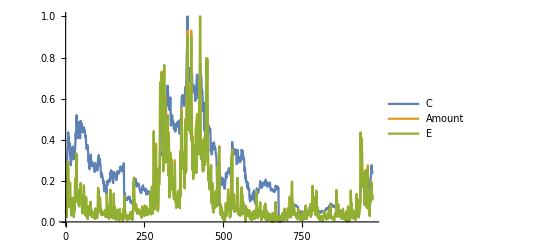

```mathematica
ListLinePlot[Rescale/@{data[[All,5]],data[[All,6]],data[[All,5]]*data[[All,7]]},PlotRange->Full,PlotLegends->{"C","Amount","E"}]
```

```mathematica
ListLinePlot[{100data[[All,6]],data[[All,5]]*data[[All,7]]},ImageSize->{2048,1596}]
```

## min

```mathematica
szmindirectory=".wine/drive_c/new_xdzq_tyrz/vipdoc/sz/minline/";
shmindirectory=".wine/drive_c/new_xdzq_tyrz/vipdoc/sh/minline/";
minstock[str_]:=If[StringStartsQ[str,"sz"],szmindirectory~~str~~".lc1",shmindirectory~~str~~".lc1"]
```

```mathematica
head={"day","min","O","H","L","C","Amount","Vol","flag"};
data=BinaryReadList[minstock["sz000975"],{"Integer16","Integer16","Real32","Real32","Real32","Real32","Real32","Integer32","Integer32"}];
data[[All,7]]=IntegerPart[data[[All,7]]];
data[[All,1]]=(10000(2004+Floor[#/2048])+100Floor[Mod[#,2048]/100]+Mod[Mod[#,2048],100])&/@data[[All,1]];
data[[All,2]]=(100*Floor[#/60]+Mod[#,60])&/@data[[All,2]];
TableForm[data[[1;;50]],TableHeadings->{None,head}]
```

day | min | O | H | L | C | Amount | Vol | flag
20171127 | 931 | 12.61 | 12.71 | 12.61 | 12.7 | 1626908 | 128300 | 0
20171127 | 932 | 12.7 | 12.71 | 12.69 | 12.69 | 689609 | 54300 | 0
20171127 | 933 | 12.69 | 12.69 | 12.63 | 12.63 | 735996 | 58100 | 0
20171127 | 934 | 12.64 | 12.66 | 12.63 | 12.66 | 557733 | 44100 | 0
20171127 | 935 | 12.67 | 12.67 | 12.63 | 12.67 | 734123 | 58000 | 0
20171127 | 936 | 12.65 | 12.67 | 12.62 | 12.65 | 1248737 | 98700 | 0
20171127 | 937 | 12.65 | 12.68 | 12.65 | 12.65 | 500698 | 39500 | 0
20171127 | 938 | 12.65 | 12.74 | 12.65 | 12.74 | 2011265 | 158500 | 0
20171127 | 939 | 12.75 | 12.85 | 12.74 | 12.85 | 1151655 | 90000 | 0
20171127 | 940 | 12.85 | 12.86 | 12.8 | 12.85 | 1695379 | 132000 | 0
20171127 | 941 | 12.85 | 12.85 | 12.78 | 12.8 | 1417678 | 110600 | 0
20171127 | 942 | 12.8 | 12.8 | 12.72 | 12.8 | 761110 | 59700 | 0
20171127 | 943 | 12.8 | 12.83 | 12.75 | 12.75 | 709656 | 55400 | 0
20171127 | 944 | 12.78 | 12.79 | 12.73 | 12.77 | 351835 | 27600 | 0
20171127 | 945 | 12.77 | 12.8 | 12.77 | 12.78 | 400391 | 31300 | 0
20171127 | 946 | 12.78 | 12.79 | 12.77 | 12.77 | 546636 | 42800 | 0
20171127 | 947 | 12.78 | 12.79 | 12.77 | 12.77 | 773216 | 60500 | 0
20171127 | 948 | 12.78 | 12.8 | 12.78 | 12.8 | 576646 | 45100 | 0
20171127 | 949 | 12.8 | 12.8 | 12.78 | 12.78 | 217519 | 17000 | 0
20171127 | 950 | 12.77 | 12.79 | 12.77 | 12.78 | 102240 | 8000 | 0
20171127 | 951 | 12.78 | 12.78 | 12.75 | 12.75 | 371229 | 29100 | 0
20171127 | 952 | 12.73 | 12.75 | 12.73 | 12.75 | 266391 | 20900 | 0
20171127 | 953 | 12.74 | 12.74 | 12.73 | 12.74 | 132486 | 10400 | 0
20171127 | 954 | 12.74 | 12.76 | 12.73 | 12.76 | 119794 | 9400 | 0
20171127 | 955 | 12.76 | 12.76 | 12.74 | 12.74 | 209076 | 16400 | 0
20171127 | 956 | 12.74 | 12.74 | 12.7 | 12.7 | 649715 | 51100 | 0
20171127 | 957 | 12.7 | 12.71 | 12.7 | 12.7 | 165117 | 13000 | 0
20171127 | 958 | 12.7 | 12.7 | 12.65 | 12.66 | 376192 | 29700 | 0
20171127 | 959 | 12.66 | 12.7 | 12.66 | 12.7 | 524145 | 41300 | 0
20171127 | 1000 | 12.7 | 12.71 | 12.7 | 12.71 | 52101 | 4100 | 0
20171127 | 1001 | 12.71 | 12.72 | 12.7 | 12.7 | 100356 | 7900 | 0
20171127 | 1002 | 12.7 | 12.71 | 12.7 | 12.71 | 527153 | 41500 | 0
20171127 | 1003 | 12.71 | 12.72 | 12.71 | 12.72 | 53404 | 4200 | 0
20171127 | 1004 | 12.72 | 12.8 | 12.72 | 12.8 | 2207764 | 172500 | 0
20171127 | 1005 | 12.73 | 12.8 | 12.73 | 12.8 | 274040 | 21500 | 0
20171127 | 1006 | 12.8 | 12.8 | 12.76 | 12.76 | 67779 | 5300 | 0
20171127 | 1007 | 12.76 | 12.76 | 12.75 | 12.75 | 36999 | 2900 | 0
20171127 | 1008 | 12.76 | 12.78 | 12.76 | 12.77 | 155798 | 12200 | 0
20171127 | 1009 | 12.79 | 12.79 | 12.77 | 12.78 | 950041 | 74300 | 0
20171127 | 1010 | 12.78 | 12.78 | 12.76 | 12.76 | 121399 | 9500 | 0
20171127 | 1011 | 12.76 | 12.76 | 12.76 | 12.76 | 729872 | 57200 | 0
20171127 | 1012 | 12.76 | 12.76 | 12.76 | 12.76 | 377696 | 29600 | 0
20171127 | 1013 | 12.76 | 12.78 | 12.76 | 12.76 | 235062 | 18400 | 0
20171127 | 1014 | 12.78 | 12.78 | 12.77 | 12.77 | 379273 | 29700 | 0
20171127 | 1015 | 12.77 | 12.78 | 12.77 | 12.78 | 192915 | 15100 | 0
20171127 | 1016 | 12.79 | 12.79 | 12.78 | 12.78 | 118861 | 9300 | 0
20171127 | 1017 | 12.77 | 12.78 | 12.77 | 12.78 | 292661 | 22900 | 0
20171127 | 1018 | 12.77 | 12.77 | 12.75 | 12.76 | 239862 | 18800 | 0
20171127 | 1019 | 12.76 | 12.76 | 12.76 | 12.76 | 170984 | 13400 | 0
20171127 | 1020 | 12.75 | 12.75 | 12.73 | 12.73 | 963062 | 75600 | 0